# Homework 2: Modeling RT

First, you are going to try to fit a so-called “half-normal” distribution to the data. 
That distribution has only one parameter, which is its standard deviation σ. 
Play with this distribution in Mathematica with the Manipulate command to see how it varies with different values of σ. 
The mean (expectation) of a Half Normal distribution is 1/σ.

```mathematica
(* note, the half normal takes the scale parameter as an argument, which is the std of the Normal *)
Manipulate[Plot[PDF[HalfNormalDistribution[1/s],x],{x,-1,800},PlotRange->All],{{s,1},0.01,500}]
```

```mathematica
(* min mean and still plausible ~350 s *)
N[Sqrt[Variance[HalfNormalDistribution[1/350]]]]
stdMax = 300
(* max mean and still not unreasonably high *)
stdMin = 500
```

264.429

300

500

Create a prior distribution for σ such that only positive values have nonzero probability (because standard deviations are always positive),  and such that the values of 1/σ have a relatively wide range. Also, make sure that for values of 1/σ that are much larger than what you suspect is a plausible mean response time, the probability will quickly get very low; remember, it’s the mean response time we are talking about here.

400

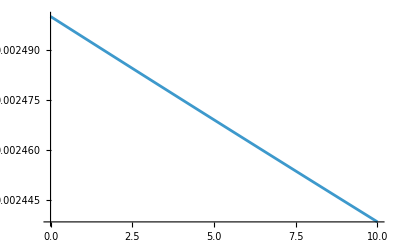

```mathematica
(* assuming that the prior std ~ Exp(1/400) *)
meanOfStdDev = 400
priorStdDev = ExponentialDistribution[1/400];
Plot[PDF[priorStdDev,x],{x,0,10},PlotRange->All]
```

Prior predictive

```mathematica
Nsim = 10000; (* the size of the sample *)
generatedRTData = Table[RandomReal[RandomReal[HalfNormalDistribution[RandomReal[ExponentialDistribution[lambdaOfStdDev]]]]],{Nsim}];
generatedRTData
```

{991.969,1742.95,168.393,487.82,4568.08,11.4652,247.258,58.2501,112.557,257.516,3.81555,290.317,201.712,82.5225,75.4235,2798.92,14.0355,47.6159,30.7755,782.832,142.459,103.139,44.1098,158.787,11.6263,45.5125,707.483,443.977,312.794,367.774,3070.47,16.98,190.286,43.0485,38.5934,252.561,589.42,2.80497,7.78037,393.64,6.21678,72.5475,352.007,276.966,1081.05,1315.22,19.6528,1008.87,8.84866,1015.21,5609.22,249.407,45.2741,73245.9,1264.75,50.2685,41.1091,41.8807,49.9162,330.995,174.468,25283.,25.0435,2728.76,766.526,28.9579,79.4411,51.081,14.9276,70.4822,50.6959,52.8797,70.427,54.4069,18.4332,391.777,47.9145,5.22823,0.14373,18.9726,1119.24,578.004,4.62624,24.5531,52.2577,757.625,58.3997,31.1444,150.021,63.605,117.38,105.158,1.8973,453.29,36.2639,157.494,742.505,118.002,1.09055,66.1904,15.5142,37.5329,426.825,818.074,106.826,3545.87,140.139,124.634,17.8947,1070.17,12.9435,91.4376,74.6089,80.045,6.55051,0.126206,409.728,107.574,87.7722,9.33,30.3567,41.7888,161.911,6.77337,1.8701,13.4142,79.7539,344.706,175.645,382.125,41.5891,332.921,2979.69,261.7,99.5354,1643.97,626.791,193.316,30.5523,18.5264,236.067,1084.58,104.254,149.294,842.26,63.6089,84.2647,37.6645,12.1831,3.49271,116.275,24.9345,744.486,157.7,91.7685,116.159,8.02889,6.42513,36.3529,0.126927,115.619,2623.31,7.65164,10653.7,572.577,67.0506,1319.84,401.216,3607.9,150.169,20.431,761.626,367.634,100.539,47.3917,84.1979,164.436,1.01285,53.0271,110.866,193.041,15.1277,454.894,90.1284,149.594,286.661,79.3073,605.629,1346.64,9.72662,34.055,412.154,514.772,669.81,139.396,1040.,6.3247,741.207,24.6585,5.21367,378.769,26.6109,6.58784,773.514,238.964,192.946,460.359,11.324,408.942,64.8754,186.785,261.671,190.802,154.664,22.2637,356.121,132.992,16.6578,62.2067,582.531,68.6103,304.184,1267.58,80.0167,107.652,15.4836,191.612,81.2823,44.7362,0.084423,9158.1,27.5074,3.90926,10.4872,1817.82,22.3228,6827.54,185.91,65.4276,1290.35,11.1025,16.6571,85.6973,834.583,6.31157,185.891,141.398,332.978,87.1172,18.9703,54.0484,4939.4,17.6806,987.105,4.81047,25.3434,422.163,931.565,311.329,640.326,1932.33,53.1559,20.7902,14.4669,62.839,19.9064,49.1366,2061.51,2150.27,103.786,53.5537,1046.67,206.138,2496.62,540.231,105.005,575.975,227.513,67.3331,148.847,32.4564,183.78,203.306,0.591803,123.96,205.241,27.3978,271.204,238.587,142.338,28.3962,17.0004,52.5373,13.1557,32.1304,151.253,1.07547,35.1038,196.698,252.662,1406.47,363.952,19.4649,117.832,191.309,4.68356,95.9364,79.3768,723.113,74.3798,236.09,20.7284,40.1012,5911.19,171.285,150.33,500.605,36.7902,964.276,453.863,55.1037,211.782,155.514,494.504,54.6982,4224.63,3.19698,22.1241,1705.67,119.977,563.761,4495.66,3.37972,55.9065,65.7805,27.8066,26.9286,2956.67,201.062,69.259,3.57203,294.72,23.4358,20.3506,25.9989,301.056,74.467,53.3347,57.0869,251.689,24.7181,238.105,105.862,102.604,1.49384,175.257,39.7666,3.52671,885.162,111.171,320.802,1379.72,18.9132,1257.09,105.35,10.0335,384.392,107.168,221.374,95.3743,5612.36,282.601,14.6823,225.015,348.619,27.679,0.17846,153.505,26.2176,343.76,1261.91,53.6441,135.209,809.079,28.5993,75.1554,15.9794,48.2353,0.376054,9.56464,25.6353,16.9458,15.8996,188.507,38.5701,32.8509,51.6134,8334.18,458.871,820.93,47.0256,72.4313,1.58618,6.08977,1071.01,152.452,934.198,24.9861,1674.02,117.476,1.09849,60.1312,140.264,120.739,9.62276,3213.42,62.8229,42.9552,125.969,12.5712,5.93996,142.736,168.282,5.17485,70.0351,23.3811,7.97054,1072.64,448.625,105.563,35765.5,3088.32,95.7861,662.425,15.8038,72.4001,138.906,11.7294,15.286,217.147,205.559,34.9232,239.279,461.599,180.356,5.60135,4.96011,4214.69,391.311,22.2428,100.225,9.33582,325.17,49.7938,50.7896,581.549,30.0337,6.67328,22.0673,24.3105,2.89609,128.174,152.889,46.8251,11.1125,354.59,68.7774,111.373,44.691,220.246,1596.43,56.4897,86.524,94.5646,41.8455,2995.57,1176.52,36.9073,18.5685,1453.39,174.333,9.85765,145.795,11.2659,19.0847,110.699,338.664,188.848,545.948,46.1952,46.9733,11.7601,51.4263,47.1991,7.54586,111.305,64.3457,82.9881,107.318,1.83626,214.678,116.168,1676.8,104.874,515.428,19.8191,10404.5,59.9649,185.312,113.625,23.759,553.891,9.65747,481.504,84.3861,10.6329,172.16,4.58239,142.491,573.84,42.8956,26.7111,2.07729,212.173,60.8338,100.818,8.18508,24.63,0.634055,369.436,757.011,2.77135,17.0363,2193.91,169.076,0.613434,67.455,22.6108,343.185,32.4095,127.069,101.956,211.547,249.685,154.836,283.979,1095.1,0.648461,131.477,67.8708,853.263,6.22619,42.2417,21.3561,8.21583,65.0157,257.348,2034.86,50.6566,184.182,66.0866,276.851,30.8548,493.833,974.892,4.04051,37.7675,1668.63,21.4902,479.839,22.1416,35.4843,55.9786,15.6773,235.758,58.3296,64.6163,107.129,525.345,77.4119,634.971,54.1573,2597.88,93.3222,491.134,379.722,123.525,28.3685,42.1479,145.657,0.26226,84.3473,273.439,1111.81,10.1661,321.571,2259.65,76.531,41.838,6.41968,1220.51,265.26,325.759,332.417,2.92276,482.107,152.823,5.97632,11.2014,36.5961,1135.36,6.44311,373.109,58.4825,209.407,67.7381,26.9009,1.66043,270.322,36.3458,763.859,15.9398,504.998,133.192,93.3826,12031.4,53.181,55.1395,10.6365,648.649,2088.81,57.7336,71.5263,5.14084,390.861,100.925,226.107,48.3262,103.886,37.0253,28.1811,155.545,4137.64,3146.99,862.923,274.496,637.819,33.2929,105.484,14.3881,73.2711,11.1995,219.202,163.478,202.216,635.158,269.814,159.455,706.072,1821.96,15.8227,9.10617,2530.97,236.025,1983.91,65.0269,12.3252,11.7115,118.084,55.0909,3.56346,85.4446,396.395,275.226,213.608,46.8681,38.7335,246.341,43.8175,223.492,199.864,19.5949,87.397,25.7299,5.64096,88.1285,278.836,22.1347,995.254,153.674,116.306,3.26137,31.4897,36.8944,99.562,216.904,54.0197,1056.6,72.8887,119.591,320.52,50.0604,37.692,5.51111×10^6,113.841,158.667,22.2791,1263.91,14.8373,22.2688,1430.13,16.752,9.36878,120.012,441.495,230.492,242.424,27.0463,46.3358,3.53976,23.669,84.6285,196.665,226.095,298.145,527.119,3.65996,61.1227,26.058,84.6437,106.107,26.7427,23.146,1049.91,43.3875,98.2229,154.258,275.952,43.2449,28.5421,83.1407,60.7268,50.5707,29.936,0.731796,56.1945,29.1321,9.95419,26.2285,482.334,21.3548,1167.29,99.9407,36.8388,282.755,1.929,435.552,466.323,133.808,218.456,40.8634,267.026,31.0798,188.371,432.065,171.038,304.894,17.3637,108.901,1.31997,1.8502,23.4208,160.536,277.253,13.1052,28.8803,195.119,6.0676,93.0209,360.207,34.1024,496.031,27.5458,109.269,38.7836,172.735,140.949,71.3715,5.73913,84.4083,266.396,10.0372,37.067,123.517,237.86,97.4003,452.749,205.376,84.5956,277.723,124.895,11.688,5.30176,3.51214,209.08,5.29989,24.5888,456.906,98.5592,72.0366,288.348,104.387,4139.69,22.4194,55.2302,90.4271,830.493,11.4837,62.9767,263.849,103.725,883.098,27.0123,39.5021,651.396,257.363,451.764,10.4754,1010.83,63.4102,1831.78,108.011,21.1405,289.928,94.5929,162.124,202.381,110.316,21.0513,103.761,37777.3,120.886,0.942881,47.4739,1.84454,4504.28,93.962,72.7054,198.517,48.5927,20.0058,315.481,1642.14,256.601,263.771,286.11,195.492,393.111,48.695,17.2891,205.107,291.333,302.959,98.6125,188.309,1315.49,39.2621,79.2527,186.295,88.3202,219.88,39.5311,3.92584,56.4852,29.8804,455.374,34.0779,294.619,5.95762,0.33749,14.0289,20.841,122.777,137.56,35.2868,220.748,82.469,40.2451,77.1946,416.404,16.2416,78.0449,329.915,105.782,137.136,172.164,145.84,363.082,414.155,49.5373,39.9042,77.9712,42.137,135.883,691.583,4062.93,457.679,1789.9,35.7696,51.9208,22.1913,3.94475,284.906,1.69776,10.8902,0.934993,383.873,11.6633,127.972,91.843,562.165,370.03,70.3766,315.256,26.0127,1736.92,12.4009,43.7111,14.1816,3.54856,179.544,11.8534,2683.56,340.471,107.403,4.35029,0.751619,141.461,132.625,274.133,58.2809,79.8267,75.5814,72.5751,56.1048,297.626,9.85239,217.558,56.692,436.744,889.961,310.342,263.944,183.221,13.8763,7.50157,1810.5,25.3819,5019.01,76.2374,365.056,35.1956,42.5921,122.752,29.3185,7.56411,2733.31,20.7803,25.2732,828.843,21.2162,110.427,112.644,1393.18,92.6298,411.944,5.12687,54.5415,18.1781,2.64657,479.433,167.057,63386.2,0.523265,308.244,0.471902,176.528,104.091,10.1255,431.894,13.1101,3719.36,7.6733,203.022,3904.12,421.791,79.639,266.077,318.13,433.472,693.675,4.42942,0.453936,142.494,14.2675,87.3397,163.389,830.465,3645.59,98.8483,38.4213,6.22818,633.069,22.6971,152.321,28.3491,705.456,3776.,917.852,74.9261,567.397,0.824931,23.1336,236.215,11.8501,170.545,88.6761,254.912,11.1284,7089.37,57.315,257.479,8.33828,126.951,0.994511,418.248,16.1772,18.0811,2068.24,12.3576,318.785,383.375,2338.35,12.4767,0.255986,95.635,193.585,2.69016,16.8992,164.232,23.6374,3.30318,5494.83,2.9456,18.8384,391.376,30.5194,6289.52,61.856,701.215,140.742,23.2765,39.6697,20.3068,2498.7,186.59,1508.39,2.71103,8675.53,734.044,96.1114,17.4632,100.134,18.7396,131.093,77.3799,1770.14,27.8975,905.37,1430.84,12.9558,152.502,531.511,451.929,79.1433,626.445,37.4253,189.08,2.34623,123.145,141.183,106.809,975.307,2.32367,139.561,474.576,6.25906,4.16299,184.741,420.78,1039.78,698.274,16.786,232.984,195.097,382.928,368.002,260.62,80.6669,218.466,57.9809,122.622,2544.35,6755.17,113.629,125.689,242.429,1141.64,71.7279,251.361,247.27,122.503,5.77341,594.515,75.6361,102.95,80.8519,26.8385,82.3147,394.763,297.027,93.9071,180.208,103.939,0.466802,47.7574,1.06796,89.555,336.026,321.73,22.7843,13.6344,25.7141,39.2359,13.4689,276.758,224.891,563.843,191.384,49.7874,533.468,10538.3,94.6948,15.8104,26.4074,234.714,143.725,36.7327,28.0785,258.779,921.245,405.774,134.21,222.548,14.5286,496.398,31.0933,4.56873,216.276,9.80442,43.3239,2226.62,186.613,16.5593,111.955,1818.67,34.0218,67.5423,25.5155,1.5197,50.9092,2063.68,387.355,339.652,29.5488,43.712,304.774,139.806,26.5328,12.4488,43.4382,197.06,3.79792,35.2646,53.4607,12.5392,1.72442,28.8559,35.5591,21.2744,49.675,9.14835,40.5791,58.8605,18.9269,181.723,19.1553,1378.81,2.03895,43.9346,390.322,127.025,50.3055,118.146,21.0891,15.2078,41.8974,856.466,246.167,7.40044,416.201,45.7865,42.7412,46.2625,142.425,340.608,11.4894,162.508,0.978511,21.5587,820.372,449.193,11.3233,95.0056,17.3087,0.9128,1071.58,34.8321,148.987,24.7809,268.806,28.1557,92.9759,4042.28,4.33162,5.87456,15.4172,31.7555,210.259,35.4878,17.0813,134.976,15.9301,12.0133,13.8812,56.747,100.782,26.0503,66.0781,63.6682,4807.68,858.439,11.8666,316.581,31.0267,43.2482,895.56,17.4019,7.54884,16.6783,42.5877,54.1357,196.305,653.449,7.28398,50.6989,63.3592,250.676,79.9224,96.125,37448.4,3671.4,142.34,22.2431,35.5742,37.0352,89.9421,153.178,35.9858,814.472,68.2759,90.6966,970.71,0.36135,70.1612,354.137,191.231,980.721,24.487,352.058,0.372745,5.84654,36055.4,3.12159,3.31599,57.5682,23.9106,307.954,49.7877,295.663,49.6857,24.4893,18.7599,15.9821,61.2326,368.178,1116.51,2410.47,45.2965,109.592,2453.69,26.4001,1813.11,14.3567,262.231,504.25,8.99405,21.8611,17.9439,17.4896,33.7316,2029.87,62.8869,25.9511,22.3726,8.32242,132.951,52.5336,377.923,62.7527,73.1305,18.305,11.6739,15.0442,103.294,9.59705,174.044,74.8347,61.622,466.109,1327.06,1349.55,20.7592,151.647,211.699,551.323,937.629,205.947,119.859,6.99527,222.622,365.399,32.6751,120.02,0.970554,79.7056,100.936,477.448,27.5155,29.6169,138.008,723.511,12.4478,102.716,1314.61,23.6419,12.2891,74.9692,7.2664,69.4341,401.989,12144.3,55.986,94.0726,47.9932,297.779,207.451,2125.46,21.9365,354.151,7.04645,82.1097,4873.28,3.5092,3214.41,93.7477,535.762,18.2115,3.07443,49.3641,66.2661,5.34908,33.8445,83.0962,270.206,93.6784,72.4233,47.2907,51.1907,5229.78,92.0019,45.4518,2222.1,74.5773,5239.62,316.267,77.48,53.6313,8.62209,64.3895,26.654,50.8174,58.8165,13.7254,127.808,3.36629,324.714,25.8592,1327.7,70.5013,21.5185,53.1563,80.7323,12.6659,82.0455,77.1795,42.0203,0.0849544,87.0577,58.5497,1.83026,32.3921,107.63,1369.68,43.5227,118.491,2511.29,3.08743,238.701,9.59097,0.265504,109.89,20.4645,15.1896,42.0955,326.576,115.794,88.1676,73.0906,64.933,24.7938,62.3747,32.0386,71.4278,209.206,2208.47,42.0202,103.466,77.2109,64.521,26.9898,19.9119,3359.05,177.155,1515.38,7.97973,12.3139,61.7732,83.1966,522.518,2.31656,4.90782,77.2071,100.841,36.9122,0.497156,279.261,285.974,9.01904,1.41142,31.4869,31.3246,213.588,8.98224,229.537,79.4513,1723.61,182.339,17.8584,443.254,169.889,64.8011,51.892,11.0875,125.748,18.4942,87.4552,33.8035,168.514,19.6697,2.5146,235.051,223.178,33.8749,166.16,43.3847,60.4762,1.12644,255.053,54.7104,149.417,0.330461,31.968,549.718,56.7357,62.8441,9.46386,104.722,80.3892,1943.77,2281.69,673.389,5.79759,2130.83,53.5491,152.882,31.7813,472.718,430.287,21.1753,128.116,1371.22,2757.12,217.617,68.7159,33.027,1.27588,3.84547,315.697,363.554,104.719,41.1121,923.797,26.8585,344.768,114.53,41.7544,2965.61,209.18,361.367,128.623,88.5965,4.16078,0.133241,60.8948,119.589,12.0828,115.121,98.4997,114.263,86.9996,42.5555,273.666,32.8648,110.254,11.5108,44.383,275.026,4.82524,30.1645,40.6992,15.866,246.445,48.0732,7.57637,28.9465,454.354,305.421,267.737,22.0766,163.793,69.6117,98.9638,502.341,2650.89,146.578,201.033,9.64645,150.163,16.814,35.7163,23.3385,80.9331,253.598,40.5657,32.8229,15489.7,26.738,4.92783,85.8515,267.044,45.6579,2.34815,201.539,47.3898,1176.76,222.406,65.0818,6.16846,12.6425,9.96375,38.0649,126.106,527.157,442.31,44.2505,16.635,111.959,11.0353,272.608,10.115,283.181,374.681,45.0892,1065.03,16.2639,31.1177,564.285,11.3719,1221.99,26.8908,51.5111,149.498,18.8654,215.582,183.761,2.19845,730.697,9.77045,523.811,35.35,795.236,62.1522,36.1466,419.898,133.974,87.0285,169.406,7.5392,196.712,5.9483,6.78577,448.843,22.5119,12.0792,111.255,170.389,99.0662,247.355,131.508,400.574,208.761,79.4034,3808.91,30.7939,227.039,143.589,27.6617,4.36332,102.921,228.289,227.28,19.9597,86.3789,67.3481,3554.98,3.75885,15.0104,86.3148,4.17841,9.94198,321.988,349.811,23.2727,2024.62,433.29,2773.06,76.4047,884.418,151.868,476.276,172.189,240.49,52.5131,4283.11,401.164,67.3311,802.867,2552.47,325.264,78.6162,132.055,6073.73,125.275,3.17594,399.945,4.32954,764.568,77.2679,3.19747,84.0868,55.6483,14979.6,40.3999,1622.21,1783.06,150.934,3953.15,44.0205,325.478,160.609,10.2654,16061.,0.353541,66.4601,531.482,316.247,6.52179,900.741,13.4357,1559.61,2.35185,17.4038,70.5896,1003.18,0.272007,31.2301,0.822841,180.592,276.57,50.1875,21.1265,464.223,180.093,3.24039,150.179,6.40453,1295.89,7.99619,86.943,57.7473,69.299,110.903,3012.71,20.7473,928.476,3357.21,294.655,493.074,57.9036,262.434,1611.41,120.213,19.8305,12.4629,284.274,11.1576,377.45,60.9691,94.7815,335.677,127.354,136.626,350.89,1.29074,7.12332,47.35,5.59746,19.9339,38.4606,20.9189,306.746,56.6505,135.678,109.578,44.1472,643.48,504.223,104.722,44.1178,357.562,98.6115,132.011,1204.4,410.957,734.031,2.51557,206.771,45.3052,40.6071,0.206459,4.10955,4.81279,104.84,119.945,156.915,62.5268,29.6366,24.5178,0.0146247,70.5876,154.346,4.10611,1739.53,17.1011,14.4078,1.06611,27.3276,149.874,138.383,2005.49,67.2004,253.486,86.214,32.8749,3268.42,78.8067,258.618,802.182,66.4337,5.67982,1.12694,4.36252,230.449,1816.34,1469.52,3919.95,217.5,381.402,295.444,744.605,488.348,33.8787,12.6199,12.3109,269.038,31.0433,33.9887,5.71864,280.604,61.3047,4127.69,1792.88,21.7557,34.975,15.1555,8.81621,71.4362,45.5787,642.579,102.332,967.208,0.167966,387.773,20.5606,1.36505,67.5928,2264.58,8.15194,312.041,126.096,145.591,92.8208,57.7644,89.7024,3703.46,70.585,1931.51,187.818,42.9861,35.7937,328.757,373.67,374.021,566.882,18.3895,93.2221,173.453,27.4969,26.8453,218.463,335.993,273.598,29.0743,82.9171,337.741,20.8056,405.349,23.5143,1853.85,49.2422,60.1571,96411.1,311.048,42.2802,37.0464,29.3435,64.1349,259.712,19.9732,2860.39,3.13567,9828.27,107.611,40.6649,374.327,17.54,110.707,1532.5,12.6989,6508.71,3.89335,9.80472,789.688,20872.7,0.31632,103.834,404.76,1.77946,58.9921,32.2301,786.197,165.48,2.87778,0.0113241,241.8,54.7284,14.5782,611.836,109.395,210.908,55.099,11.1122,166.887,69.5547,1524.23,213.342,468.444,354.048,27.7844,19.1406,73.9205,275.366,7.71391,451.319,190.751,29.3722,65.4479,131.329,207.84,193.734,19.6628,14.1488,21.7771,357.033,12.8026,203.714,179.149,94.6581,221.619,22.4111,68.9777,466.392,2.22533,157.923,27.9196,66.3408,80.689,12.2492,40.4123,58.9272,17.6538,3.74721,117.537,1860.63,31.6438,4.69487,3263.78,20.5622,78.3799,4.78991,439.827,44.778,1523.48,59.0335,175.276,130.688,146.21,116.972,59.7201,24.9281,5.45723,12766.5,47.1682,46.339,38.6402,24.8785,217.681,383.862,61094.9,264.205,296.989,2070.14,16.13,107.165,217.42,621.79,120.275,162.044,97.9093,2217.2,107.114,137.611,105.552,157.226,3108.62,4.32955,38.3403,122.907,505.293,97.0289,47.3077,19356.,38.3412,30.5084,69.2483,11.961,1351.81,2.25393,74.0029,716.419,38.7474,152.685,26.9942,161.134,20.2802,259.51,94.9923,2.31702,81.8998,0.449849,83.9501,14.4877,37.494,153.144,22.8766,122.567,1590.52,590.915,169.466,10.4907,59.1218,28.1794,89.7014,128.599,62.7586,66.9058,41.0121,68.7142,11.152,369.958,51.3562,51.1777,754.814,17.3149,16.5456,77.6149,126.827,33.9697,1437.21,182.049,3.62682,83.1549,29.2627,279.536,31.901,1.78572,170.071,218.413,44.3013,236.733,1181.88,42.0713,85.8546,71.8007,76.214,0.815286,650.398,27.382,17.161,94.1013,10277.5,198.449,121.157,10.7233,32.1585,72.1734,13.3714,114.544,637.247,0.597501,146.868,177.935,1134.06,96.6303,169.217,379.66,3.21011,4.98633,125.723,34.7796,47.7654,28.389,94.8517,429.849,20.1177,217.831,2225.83,132.339,92.7784,3106.91,196.574,180.416,73.3898,687.125,105.052,2.67678,1125.29,57.435,28.9607,509.11,1.91163,110.167,76.2803,16.0275,94.9974,279.481,73.2044,1458.42,471.77,380.078,24.8454,252.797,577.049,61.6732,25.0102,27.3827,207.022,64.4197,1110.68,362.27,32.2928,79.1441,102.118,451.391,98.1277,868.039,56.6785,48.6873,2.79809,9883.72,470.153,0.980189,0.312931,247.029,1.61516,90.441,30.061,119.345,73.5007,620.304,42.3685,524.593,40.3437,5.25811,517.32,50.9358,39.6174,235.492,1259.22,46.3108,134.395,39.3748,381.566,148.883,22.9171,55.1848,8.81582,158.1,697.242,44.8816,301.327,84.5673,114.43,17.0047,168.186,459.934,281.215,1.31108,0.726502,4553.97,16.1118,79.6737,68.1002,124.529,37.541,11.8411,18.9504,29.7396,132.669,11.568,52.4768,6.16875,1.90672,20.9715,254.529,9.14302,774.032,47.5302,532.723,1082.69,205.572,154.976,101.677,217.288,33.1597,257.328,132.628,95.4404,20.146,14.2011,38.2908,194.453,150.675,16.7378,179.885,68.2516,177.977,725.135,192.311,3039.31,154.172,27.124,48.7984,197.466,355.776,23.4859,115.555,194.5,144.842,155.583,183.739,71.1052,173.964,709.883,62.3078,14.4714,47.3072,103.462,15.2576,147.694,154.341,474.564,36.3098,724.965,70.4798,18.7554,4.31124,524.551,77.2924,122.166,438.639,1282.08,322.01,54.3659,96.7993,53.5098,50.9261,122.04,13.4604,133.261,8.90966,29.7092,373.007,59.6273,49.6923,3.34746,127.069,499.316,307.659,1863.46,348.882,0.916724,507.15,2.93969,235.247,135.931,48.3554,1.23721,1290.24,10922.1,146.105,935.929,37.1647,5.12036,1037.39,69.3191,65.4375,428.879,45.1944,1295.49,57.8541,181.289,191.583,16.7824,5866.39,228.339,310.242,96.0171,47.1932,31.2803,69.2038,25.6765,10.5379,20.252,223.39,152.535,208.791,0.693801,163.409,147.092,236.76,3.20465,156.505,279.657,531.768,292.405,10.4108,6.22854,247.003,421.173,15.3335,57.3724,78.1432,516.622,11.6399,3.67278,530.966,395.356,89.2268,9.22242,87.3144,73.5314,50.8221,573.477,69.0609,93.0286,1182.27,129.291,0.988052,187.699,428.445,459.741,797.366,761.496,76.0142,364.947,281.748,47.2888,114.9,58.8588,40.0243,43.3537,1213.17,1242.16,221.323,227.054,3.71033,25.9237,654.785,116.449,728.743,226.002,205.071,295.18,841.214,432.41,370.336,61.0707,16.4096,9.66696,29.1431,30.4691,22.3008,86.1223,105.431,99.5347,303.361,89.5356,154.759,1591.64,140.306,121.735,165.356,18.8905,8.23574,34.9213,13.8868,2.07103,1.90443,172.829,9225.67,58.106,13.7373,82.7476,0.709054,219.259,40.37,9.70808,178.932,1.43632,10.394,0.0754732,0.20082,653.587,146.964,176.084,3.5199,52.3734,123.243,68.9047,565.022,151.717,993.484,44.7514,4.407,690.435,96.6012,49.6708,1610.33,21.4856,384.718,24.0714,34.441,0.780046,50.0597,3.06548,217.398,213.518,162.962,401.126,1123.45,6.78314,7.91099,19.1412,26.2709,48.6692,219.497,717.104,374.788,289.173,131.922,236.858,2.02009,106.213,1.68485,876.686,332.209,140.971,19.4466,67.295,75.2222,73.7582,222.921,117.889,44809.2,145.806,133.404,14.2632,2322.7,267.087,114.039,3.31318,59.574,34.3666,41.0447,68.1871,533.037,23.5143,147.521,3.14474,394.157,50.6488,48.709,12.6758,1.9856,1518.7,9.78303,115.819,4.00996,30.7192,72.3899,8.72363,681.385,108.461,129.766,0.443093,209.834,91.5216,16.9387,0.31449,43.1253,523.194,223.169,28.1507,17.4944,4.20626,74.56,107.97,271.716,85.0775,237.724,146.476,65.1179,170.759,289.776,102.381,6606.59,39.2012,213.974,32.9438,11.3318,90.6199,1374.43,332.532,12.3727,99.4353,14.3725,356.121,390.016,632.003,71.6785,23.931,14.0457,24.0804,2994.7,17.7772,28.2635,72.5609,146.79,11.6801,232.097,79.7566,2.43381,15.1004,13.9954,6.69763,402.641,215.304,590.203,53.7994,52.015,499.675,2.63025,537.991,88.3101,1130.13,76.0681,115.885,142.822,159.727,174.07,17.1251,194.235,5.80398,662.005,608.439,94.3118,7.12584,419.45,22.5874,1414.37,38.306,3354.19,3501.04,5.32487,39.3162,144.738,111.51,20.2247,469.318,293.72,7.92132,2.24409,1255.01,457.194,429.413,20.6101,6.11438,229.402,147.074,205.44,514.238,0.228895,10.0969,16.6196,104.12,90.4225,152.424,50901.2,40.9916,18.5181,0.0975172,71.033,1.04456,115.172,7.69602,320.211,235.553,111.794,248.471,56.6289,145.51,107.125,236.245,264.998,142.604,17.9155,0.468655,651.713,717.121,4978.59,30.3446,2213.04,22.53,197.183,72.4222,75.3939,2286.16,360.706,61.7439,72.7532,256.833,35.8576,154.38,43.8697,167.544,538.989,1.93805,1648.22,367.542,2435.47,271.167,57.4769,1045.1,0.581879,70.6616,38.9039,28.5503,7.85258,278.989,4.40069,157.454,22.7746,221.8,12.4536,7.83743,460.845,29.5803,44.28,3169.26,135.35,129.555,243.133,2415.23,1392.09,363.51,357.532,720.298,6.02478,665.515,46.3843,307.903,9.05084,183.542,45.8299,63.0398,22.4675,18.189,235.423,162.885,254.142,55.3501,439.17,45.585,57.9909,52.1114,0.255469,22.2239,9.30725,857.717,158.049,10.6032,381.524,91.4089,303.483,223.325,4.52041,7.62288,80.0494,402.526,1050.68,721.266,202.398,370.324,241.354,129.64,107.228,8.53045,3.11679,44.9842,22.4119,245.282,215.915,258.325,92.042,4.48207,722.06,84.997,68.2211,5.48996,52.1897,2208.18,1.06374,46.1269,27.1321,171.471,1491.81,300.168,528.973,106.16,793.986,2234.12,40.7322,80.7984,20.3553,59.922,3533.16,0.00474848,8.95281,72.4049,915.844,29.7899,2.82415,16.1268,23.1275,198.734,12.5881,77.8556,74.4721,10.1815,16.9004,47.1479,165.527,12.4488,2.16198,112.475,15.108,1885.99,32.6434,210.956,9815.02,420.117,313.64,205.611,38.2479,9.43383,36.4424,24.0501,13.2154,185.158,35.7897,20.9865,142.748,277.167,480.424,438.891,257.634,663.197,113.3,11.0353,65.199,109.83,7.06863,87.9862,499.227,348.137,314.788,3.68451,4.30127,64.2434,4813.16,663.419,40.4306,17.5494,69.9391,16.5182,93.1249,566.615,149.558,10.6418,1359.61,63.5591,5569.81,66.1757,2919.64,379.573,35.5767,542.038,78.8727,28.8324,123.862,24.46,419.165,35.8048,207.385,435.912,203.334,163.524,1497.17,95.4287,188.156,46.9891,4.45579,110.676,234.658,811.962,31.101,785.77,19.2116,2.41366,61.3172,230.924,32.7714,27.6036,88.687,16.3509,20.7183,32.4008,1325.74,64.7181,25.2749,118.04,269.535,278.035,28.5941,53.165,575.059,618.582,0.0480723,22.8148,434.566,1141.29,0.390641,47.2041,198.105,552.086,154.108,452.697,779.029,134.403,0.431848,16.5523,1633.19,2040.93,74.5654,97.3821,156.495,243.734,148.464,287.27,0.225561,245.296,2.32549,11.6926,138.007,176.611,23.0425,132.179,74.5131,50.1166,3.34467,2.94656,8.5078,994.566,427.984,0.311512,424.159,91.6932,446.045,10692.6,30413.2,85.4783,181.993,20.1499,113.677,27.0083,56.8745,1145.2,157.418,13.7693,689.865,143.612,67.3829,3.08809,70.0946,118.857,48.6313,322.08,128.941,26.3796,4.15311,132.782,1.7279,10.7101,1.01766,11.9638,629.665,360.346,132.266,35.8345,220.384,330.665,122.156,212.519,32.229,866.246,1231.14,200.25,97.1382,32.7993,50.2053,33.6409,3.08709,1203.58,21.4437,32.3129,279.578,138.218,44.0691,186.92,48.6221,122.058,49.6287,2480.48,83.4303,883.797,78.432,68.8911,63.1555,589.323,198.242,9.76935,8.64555,16.7928,1.88151,75.5759,63.6516,1.06215,270.115,149.821,131.177,3.45783,871.069,44.1524,77.7244,104.418,933.802,331.074,2117.06,1342.19,99.5435,2.92487,35.7497,594.457,434.06,3108.92,23.5311,394.267,1900.6,113.386,398.059,20.1808,28.8174,30.2447,645.208,13.8704,13.3921,22.8303,17.0071,155.239,29.0765,29.2369,11.4203,117.719,14.3968,188.429,79.9366,65.1858,55.0762,75.2596,60.4456,101.597,131.017,78.4568,362.726,975.169,481.94,1174.35,16.8941,125.451,89.443,25.3923,97.2489,1553.13,189.236,867.343,299.418,105.097,1401.31,179.832,35.0197,147.732,66.5439,8.92794,107.867,5413.12,202.063,153.26,4.18355,32.7133,79.6185,17.6024,95.9382,56.6904,1191.77,7.95811,172.766,13.8732,1165.55,391.943,42.5842,24.147,31.5297,3.26305,1964.29,558.488,12.5659,11660.7,8.5956,9.20919,506.559,59.5703,782.003,65.4327,365.311,164.413,321.259,310.413,197.554,262.969,2.48154,82.4672,203.512,1340.71,31.0419,207.037,194.762,20.8793,548.119,9.38194,383.142,45.3822,55.5274,720.261,3.61763,402.6,423.882,1.20188,2.50083,78.5705,9.89983,1.2655,70.9503,184.564,56.4251,118.732,6.99577,218.61,19.1566,160.095,49.1162,75.8415,7.15004,145.304,70.9291,16.2243,415.853,387.212,9313.57,396.52,13.5007,593.475,15.5928,11.0206,75.7625,134.217,101.626,208.759,11.2526,210.018,135.829,175.529,94.5609,161.333,71.743,71.7572,329.895,1528.8,104.152,123.555,31.668,2409.74,174.988,436.94,13.7051,1967.32,67.5331,1375.84,497.227,60.0516,148.205,82.42,59.8681,3.83602,595.854,10.9198,33.385,11.3034,256.425,1454.12,103.521,1.56122,304.78,173.951,217.818,405.415,2.91459,63.6494,61.1886,24905.7,57.3562,283.592,84.387,136.82,7.3771,9.47878,21.089,662.448,2843.84,780.037,163.002,24.9722,246.274,27.8279,335.577,133.514,1.35286,46.8476,14.5842,0.732566,14.8403,239.289,218.223,539.07,23.3753,76.2106,6.88294,0.915725,31.8025,49.8066,41.8821,1110.67,92.6647,112.069,37.0475,26.5712,50.2265,20.8999,3.98155,6781.21,2019.86,83.6216,26.9559,49.2387,84.9957,7.35095,32.1955,218.529,75.331,45.2119,65.2341,186.32,20.9273,9449.44,237.898,289.876,139.249,0.319979,12.6549,18.3552,379.024,67.5276,48.9813,10.6197,15.2832,25.4371,216.892,72.568,242.644,1005.31,5.89654,22.0816,471.531,0.410757,56.2028,4.97424,24.7812,392.94,44.1992,9.25225,837.151,2549.62,261.375,46.5463,2036.24,37.9296,113.658,393.007,753.474,1227.77,0.882354,135.134,138.123,335.31,80.2231,46.1714,180.332,39.3866,246.042,16.217,42.7491,289.387,1.04722,325.692,137.595,8.13731,39.5661,134.522,3.87264,2.54357,10.577,22.597,474.628,169.365,16.6683,214.72,144.513,897.724,2718.28,6.61559,257.931,7.45092,24.7588,12.9723,938.464,91.966,250.638,184.553,7.4079,7.78135,21.4049,43.3696,206.307,35477.9,180.878,0.116014,114.07,832.34,3828.1,101.412,54.7597,2.80217,21.8134,46.4496,68.5796,3101.18,681.602,253.778,0.266772,6631.63,371.844,247.419,31.0472,237.332,263.775,36.73,249.361,204.702,328.58,44.217,147.618,147.276,435.922,27.0123,1286.85,336.32,4.19475,24.6045,0.46084,97.8102,416.827,244.545,434.548,631.118,0.661752,75.4982,62.2603,257.974,249.163,111.83,3940.28,26.0526,183.417,7243.37,132.774,56.7263,206.261,132.959,143.448,2364.19,899.173,46.1733,5765.78,8.74813,42.7153,10.9689,1090.34,88.8049,34.2961,424.087,43.0766,153.944,97.5926,12.6843,6617.48,95.3506,335.202,1354.67,54.7947,671.912,24.251,516.401,63.3062,187.915,105.342,59.5585,1538.07,63.105,71.1458,541.132,80202.,9.6559,1053.65,99.3256,830.081,451.465,13.7096,15.5838,7.41786,43.9324,4.73841,5.43475,51.0875,63.4961,13247.1,131.78,116.47,409.242,23.0351,1178.52,3.26045,2963.75,132.903,100.814,7.95608,22.8441,546.783,150.498,1324.08,462.853,38.2268,23.5569,231.426,419.973,22.4419,66.4838,114.28,10.5202,358.81,6.08405,14.489,33648.,479.385,10.1848,227.5,118.608,18.8859,31.7767,268.16,34.4734,140.677,77.3089,131.47,326.867,1.86477,146.602,86.8115,1049.44,88.7033,158.488,177.689,274.768,16.3467,74.0239,237.427,0.42829,917.167,30.3945,143.701,156.931,2.2442,246.724,124.233,217.425,2293.58,4.43811,12952.,7.74352,4.39364,56.9608,3.05367,2092.4,1.17714,4409.15,128.604,706.498,146.783,1114.81,167.664,26.9581,8.53479,590.45,4.02019,41.1065,33.6123,38.0498,154.875,268.945,866.707,19.0631,53.7365,196.789,424.286,672.926,48.7039,61.4775,373.083,2.17014,43.7764,7795.78,25.1797,4.63089,323.927,2.09956,130.491,530.327,226.374,28.0098,6.02375,1235.62,48.7242,76.6086,20.0649,25.7654,156.441,146.392,634.007,6.05318,23.4484,4.08264,114.952,28.6304,18.5658,384462.,39.5009,2.24404,784.944,6.99001,159.469,170.328,89.8153,116.897,301.606,6374.56,2.76204,239.049,297.287,452.387,378.51,80.1351,10.7153,3.43083,101.046,745.69,1.83408,9.17691,93.5722,5.55181,91.4669,1.60539,20.3546,112.776,6086.09,126.284,19.3266,0.35473,39.5622,235.765,7.26449,41.2291,44.4469,74.2515,506.495,342.244,61.6478,17.9116,70.1639,985.022,48.2277,22.2827,0.798635,367.624,388.691,42.0739,29.4706,117.492,7.60327,103.788,47.0903,435.233,28.8843,14.709,2647.96,516.661,9.30408,240.691,55.7944,78.2244,72.8615,116.672,277.936,201.915,15.4814,0.45828,765.865,873.735,155.722,59.482,4.89082,5575.58,58.0382,438.065,135.526,3594.56,47.4626,175.945,40.1655,0.196541,183.593,779.461,13.4345,276.596,10757.2,20462.6,9.01023,62.2023,152.004,61.6787,117.931,37.6321,2559.32,1580.81,462.885,111.678,221.963,184.054,11.6387,62.2525,3.96415,237.23,3.2084,263.392,48.3022,0.647038,37.1368,143.544,77.2108,49.0113,9.46631,1.64213,705.877,1308.56,90.594,24.7959,29.5028,81.7816,921.024,201.724,41.4591,32.313,11.4043,32.9757,70.5706,513.495,146.156,1293.87,1.34461,174.283,0.526836,247.395,251.087,20.3525,92.5644,188.415,157.338,100.426,229.852,85.6234,51.6693,131.177,403.795,9.69011,22.6207,42.4011,1076.,224.821,520.073,1.10186,131.879,26.7419,45.1956,1265.56,10.0343,100.804,1664.65,29.7364,152.508,184.859,16.4284,51.8199,204.1,34408.4,10.982,1.52622,94.1188,10.5601,152.393,271.092,65.9464,18.9791,537.574,281.902,25.4349,28.3129,25.6478,13.9276,352.628,1956.83,7.56668,76.6291,127.552,466.971,67.5931,2490.42,260.557,11.6022,19.5471,1083.63,2981.39,1231.33,2507.35,362.377,257.935,110.21,226.986,5.37394,5.88887,385.424,95.1145,127.238,33.1276,56.8484,16.7122,100.008,306.429,72.2034,13.2446,446.491,49.0098,38813.7,14.2667,0.922064,673.77,52.6993,220.9,84.3189,106.068,41.2331,545.775,649.699,274.404,264.049,280.653,44.1847,623.436,236.479,364.195,1259.26,26.6886,2520.82,40.7391,1303.27,125.797,37.8391,46.1328,457.661,20.1317,10.2144,6.54441,422.323,39.8709,6.07725,13.6832,336.1,14.8892,79.4727,193.663,883.215,369.748,162.396,5.20498,81.4899,133.009,4.45028,32.7798,139.47,102.839,11.6975,240.449,2123.21,820.83,604.328,30.6698,163.711,12348.8,79.7782,302.765,461.363,58.3475,11.1411,160.905,1296.31,204.434,11.0243,181.966,169.838,907.022,126.105,9.55168,55.071,1.39087,17977.9,9.21128,58.4051,144.526,473.552,53.6342,66.9906,775.203,2927.,67.858,24.1156,819.034,210.819,11.0805,118.071,421.937,1552.2,19.3629,26.1705,225.811,480.835,35.705,192.766,640.067,25.8603,63.8239,801.273,119.394,34.8705,51.8757,49.0547,44.8024,600.797,26.6101,110.124,1205.47,105.572,32.3936,29.6804,1188.09,336.658,766.085,200.001,55.4134,14.3156,197.575,41.9796,208.318,0.732038,237.447,163.143,208.536,47.1471,384.131,355.854,24.6347,363.56,50.364,92.8064,59.1904,16.3827,62.9452,219.514,129.646,20.0461,10.2536,20.8503,77.2912,152.94,16.4434,15.5088,74.1907,70.6112,21.3003,48.5508,188.942,126.296,4.97861,5110.2,1727.73,239.686,223.46,7.87079,5243.98,37.2989,62.0035,1354.96,10690.,1.39958,155.606,363.003,95.6576,178.501,148.017,436.403,173.384,80.9143,169.608,77.6786,165.752,198.159,139.004,75.4405,567.615,0.800128,6.11233,4188.24,689.295,119.545,20.6709,144.983,55.431,36.6707,75.7198,302.504,1608.07,0.0444703,15.5225,26.6409,19.5744,452.33,458.2,1343.81,7.46314,180.113,1362.83,36.296,5858.44,142.475,90.4253,5.55001,349.048,31.2481,150.496,55.698,11782.5,72.1734,3.79861,103.107,12.263,455.15,54.3606,47.6339,6136.11,76.1651,198.019,632.932,644.829,18.2325,90.4988,78.6226,123.174,130.19,450.094,225.234,20.7981,1.44162,61.7689,36.0104,214.885,11.9064,126.761,35.616,149.409,110.043,134.2,2.6462,174.544,49.8234,37.7023,36.3684,295.672,234.304,92.2626,10.4244,42.5944,1.55271,529.595,17.7454,1657.59,11.6498,106.224,32.4938,18.3093,244.434,236.024,92.6969,400.887,628.994,78.9439,17.9944,22.1081,0.211461,155.818,271.024,188.091,2.42647,1.01584,26.8695,247.32,212.839,666.742,502.863,115.217,97.7305,374.331,105.9,389.617,87.7143,120.044,55.8596,166.795,359.532,212.565,146.709,112.513,279.18,99.7899,0.662641,131.476,111.598,2.09175,1.59315,63.8824,314.66,63.8964,49.4194,3729.52,25.0774,34.8003,14.9405,167.988,2308.89,4787.2,409.525,719.451,4.14397,510.013,596.908,1176.45,418.097,16599.8,151.148,103.13,211.24,21037.5,161.135,825.767,3.73379,432.074,24.3766,2801.6,291.556,79.2197,161.279,115.22,134.088,80.4199,101.175,104.735,23.8811,18.9583,17.4059,4972.16,101.356,133.626,116.309,1145.9,2.77683,867.832,70.8574,454.704,115.85,40.4635,91.7466,4.61728,9.72109,269.985,159.591,1795.29,97.6833,1243.26,31.5503,159.931,82.485,34.7095,444.26,121.773,17.3692,241.792,1875.31,5556.72,424.295,251.9,165.266,59.709,7.11758,144.669,89.1517,262.827,121.738,1428.61,24.6247,138.367,23.2221,39.1693,399.718,491.679,49.2549,221.161,156.437,190.486,359.961,0.3835,13.1903,4.3449,198.719,84.0988,92.3812,11.0238,15.2474,111.407,27.0614,211.059,178.31,51.6184,47.9415,55.7294,16.0358,163.98,313.38,171.987,29.9124,579.255,117.389,89.5429,173.926,57.2946,743.851,48.3055,38.7659,195.556,346.29,967.809,18.9532,4.37989,70.4461,43.2457,44.9096,157.344,69.4047,1.84349,113.802,61.7778,204.368,0.19424,2.33423,161.833,34.5112,257.815,201.037,197.378,3633.34,41.8532,257.587,218.057,247.55,863.946,0.442214,3.9105,17.5923,510.559,20.4775,102.386,46.9237,53.9574,48.8417,623.924,190.321,14.3037,38.3906,73.7839,146.699,2304.77,0.0227079,5.0958,69.2928,48.2524,522.375,38.3483,237.543,13.9086,38.7809,766.569,124852.,1215.2,43.0811,74.2565,239.688,165.231,2.4487,86.3157,713.084,77.5796,9.44968,158.425,62305.6,331.746,62.9856,127.059,97.608,32.7335,0.503155,4.592,19.1701,211.579,52.5314,61.71,376.529,2294.9,32.0405,87.2885,3.01665,1.99693,44.0857,64.9644,660.302,1240.74,21.4787,364.938,489.578,116.245,33.3255,567.346,38.1716,989.432,35.6282,1593.13,99.2324,56.434,2957.17,165.794,285.841,51.6254,26.3302,88.6795,4543.13,2211.71,56.6783,136.007,188.484,17.0926,8.59352,1575.84,4.81622,414.163,17.7952,15.1316,395.533,79.1281,16.5304,38.1114,468.772,12.0397,2.59896,22.1931,625.433,33.0327,176.599,353.399,5.73358,67.5114,88.5976,63.3649,191.803,30.3612,31.8638,615.234,235.108,28209.9,644.949,12.3062,188.7,354.108,143.307,172.697,361.196,26.3649,1200.24,152.852,1451.7,84.1759,11.8771,15.4167,37.3656,170.302,53.3566,365.924,26.2301,183.229,13.8508,245.656,43.0146,24.2152,549.82,46.7305,47.062,36.3486,669.788,540.926,8.20092,48.6135,2972.51,23.2532,1031.08,18.8884,278.976,22.3802,193.61,260.782,38.8649,6.40079,241.206,1207.86,141.672,20.3509,227.002,397.238,477.833,390.122,125.074,768.263,0.715461,72.0814,87.0052,130.447,31.2041,89.2644,5.8068,25.621,759.77,244.435,5.44323,166.963,4.05188,60.4276,2189.12,19.5008,118.784,72.8397,65.2503,3.4377,146.622,246.426,4.19869,66.709,1579.36,22.049,19.591,1019.11,28.2137,96.2463,537.445,61.4988,3.8875,57.6284,48.7274,358.292,6802.13,140.301,0.652792,304.789,2350.75,30.8102,5.08946,502.631,51963.6,121.371,1945.11,73.8327,24.8991,151.193,1380.7,88.9843,158.267,6.22381,26.4492,30.0669,151.638,104.891,12.1944,21.4647,1.25831,191.355,359.884,37.7353,6.14533,106.19,281.349,5.575,14.1948,251.261,11.8723,14.3261,2424.39,66.6279,204.86,120.769,152.855,140.649,101.538,104.949,1.77802,11.797,75.3749,177.596,566.007,203.909,69.7047,73.148,93.3972,316.742,28.5854,243.124,379.454,39.4757,153.773,22.196,59.9382,74.7674,8.67105,26.6669,5.56701,123.198,12.0194,686.578,383.414,20.6856,522.136,106.302,7929.41,55.6594,53.7441,4.07509,248.889,38.6145,130.412,57.0618,492.838,39.6499,75.6354,1367.92,13.3557,1.76528,36.892,36.2115,197.666,118.751,1007.39,0.148519,298.396,529.097,50.5091,95.4905,1741.48,69.2393,202.563,3553.03,59.7049,185.753,45.8801,101.464,22.1106,70.9331,11.1673,296.529,25.2211,0.348736,155.093,34.7359,748.73,168.732,121.49,230.068,4.74239,268.425,2.79086,0.312533,202.564,15.8788,33.7941,125.803,501.699,48.5437,3729.32,145.704,55.7065,69.8474,1517.54,7.54966,78.2521,2466.25,0.246306,65.1006,20.1683,27.6495,417.817,1085.41,36.3139,63.5776,4.60615,95.9905,425.13,825.573,25.325,22.5273,1476.31,100.742,233.081,185.987,120.74,1150.97,37.1329,0.805688,209.658,217.907,48.5726,14.8889,160.716,241.548,0.111492,196.561,367.074,53.0627,29.5143,141.736,2941.98,6294.37,229.581,8053.11,206.902,1027.4,95.3949,1100.72,363.072,3705.28,221.403,75.1439,43.5459,1102.17,102.743,1271.55,509.175,55.0033,56.3466,4001.8,136.143,4.45823,118.736,34.3581,26.8141,958.14,79.3412,504.381,19.6505,37.113,448.855,1519.55,51.9437,32.3545,178.022,17.4697,67.7952,49.1398,55.5899,0.287527,56.0585,1196.04,51.6537,187.007,52.6791,147.61,35.1891,96.9557,31.1368,57.6867,1413.37,312.269,114.515,235.921,39.392,156.04,169.07,0.532102,794.204,227.973,21.2376,43.5996,46.3346,104.956,37.8699,0.332626,68.0616,4.3816,4.83206,238.863,167.466,486.461,31.0239,157.01,228.301,39.8873,135.326,700.535,37.7674,3350.91,87.9618,46.9311,48.7417,6.01281,11.6841,71.8569,223.338,53.2282,21.6155,53.8838,63.1583,77.7981,36.2381,280.781,1783.6,554.286,32.1389,7.69575,181.035,1518.35,2.56021,214.946,246.927,18.777,560.582,12.1745,200.322,78.9545,34.0461,1472.11,1.07382,301.045,24.3302,94.1231,89.3907,26.7247,34.6393,140.381,2180.16,2084.04,74.7307,147.449,290.638,95.1834,68.4168,1328.49,1.08448,1539.46,0.192283,94.1622,4.84519,100.26,406.647,53.3497,2001.04,2.18131,319.449,2287.08,2086.4,50.7008,112.797,205.985,16.5506,56.5805,17.8731,12.9298,51.5904,141.821,5.23893,776.506,60.8206,6328.24,824.48,6.87825,107.343,52.8849,1042.44,78.2528,27.6577,96.1126,70.0152,115.324,831.869,48.0028,3.55046,387.554,3.19931,144.359,417.808,80.0606,381.409,464.896,37.655,94.236,47.5845,37.2168,9.22901,3.85213,0.397647,538.479,22.5664,1118.56,34.1538,145.269,55.5216,163.885,381.391,164.398,106.281,422.408,663.033,13.3075,140.073,172.208,844.433,3.41596,120.443,295.901,21.2169,1591.8,19.3385,74.9583,11.1813,3.80632,2855.83,1888.52,492.359,57.3039,195.048,225.027,174.628,6.03032,45.1134,27.9163,0.702348,239.713,121.093,12.4682,938.047,1091.65,36.9834,282.742,140.808,208.858,1119.27,364.591,9.45275,228.077,17.9934,66.5844,3.43827,1239.27,138.402,26.9444,256.097,192.005,141.196,623.46,879.,73.1665,218.771,5.7957,491.412,7.44233,714.988,321.002,14.4802,0.485351,4.52082,35.147,5.21005,16.9751,39.2492,24.2143,30.8523,5398.76,49.8248,295.897,213.956,412.323,522.362,27.2943,401.891,6.25987,227.292,26.6287,35.0921,62.488,105.747,2.08389,248.465,22.1901,84.0176,152.335,77.949,362.073,86.5253,23.927,21.5877,111.238,0.215326,352.683,1379.69,157.568,47.6774,99.5722,1297.39,11.0689,86.4381,74.3325,186.343,56.9799,115.343,50.1945,5.19297,60.6045,664.004,112.366,4.29162,50.2247,0.0796459,730.254,31.0895,285.198,27.2365,447.243,1546.54,11.039,25.4197,172.389,2821.99,50.3442,3.10776,3589.56,126.939,37.3196,16.2033,37.6571,75.622,18.5975,468.27,3.56207,387.47,29.4082,178.514,55.4317,29.5765,11.3213,46.9007,151.657,17.2867,494.276,0.178859,104.967,147.36,357.287,579.016,84.612,187.192,30332.9,221.236,8.47174,129.638,4.03411,1.51296,47.6982,1705.52,10.1752,25.7379,781.901,212.122,1.58407,24.1202,157.893,74.7765,14.2885,48.489,523.061,135.254,22.3451,71.5999,202.45,723.694,483.169,24.7414,1151.98,47.0212,48.9641,11.8627,137.744,15.2546,145.941,6221.35,4.11698,166.075,5.06353,1137.38,60.8219,641.875,99.4485,23.5352,244.315,24.6281,348.465,49.3548,1278.79,2314.68,7065.66,850.508,214.546,50.5525,326.062,6263.63,5.19284,1236.31,44.1248,39.6324,223.435,20.1293,202.745,1511.42,335.341,200.988,30.8854,126.723,124.326,301.776,565.92,42.4405,312.674,14061.8,95.7531,26.725,68.415,4.09072,71.9218,5.03471,496.164,20.1965,660.446,128.474,24.1098,377.116,41.7446,100.011,51.2574,798.362,14.1794,44.0348,14.4575,95.3318,17.6937,81.0356,5223.11,353.522,12.6822,11.7672,5.86316,90.3166,12.667,132.23,542.112,5507.39,1431.41,31.4777,55.8859,85.6681,1580.99,16.8494,29.4436,86.5163,317.851,6.2945,10.1618,6.20579,426.958,67.0908,160.17,214.864,46.8028,72.9942,4720.03,422.92,20.8421,127.119,1204.79,29.4271,14.2247,5.25622,2.70397,262.175,24.5797,408.073,18428.7,63.7639,335.167,5689.49,1663.75,100.444,1469.66,2.47038,935.462,520.916,763.519,3.28707,575.366,2.60283,31.4612,0.338358,2105.4,0.453956,466.282,449.288,269.738,166.179,625.474,88.6898,75.2745,6.42075,6.85206,68.4105,185.783,2416.46,55.1726,8.27114,434.291,1199.68,1496.19,29.5857,6351.87,16.8053,58.353,146.897,130.793,263.241,9.8683,4073.75,383.174,148.019,318.45,540.725,108.371,215.73,37.4138,237.058,164.569,333.212,32.6549,46.484,506.854,43.1662,33.1643,30.3161,34.9563,372.979,1061.85,110.863,964.538,137.395,33.2043,94.0388,5.90894,111.215,67.1914,675.697,10618.,54.0587,10.2185,8.08509,4.69405,15.4079,13.5866,144.343,130.233,49.2688,144.808,11.2844,88.0178,303.822,875.803,88.1415,111.182,18.0197,1353.71,79.6292,0.0416904,79.9638,0.176956,21.2786,80.1587,227.1,115.079,27.6353,5.13725,534.796,9.95818,92.3267,100.107,166.314,92.6118,2961.17,395.587,51.1788,35.9852,1481.38,225.16,325.706,81.7326,268.156,709.863,503.08,186.622,133.89,2.69184,125.761,21.6001,10.7325,357.883,15.1035,48.6958,9.15206,278.5,2.09182,49.8725,8.02076,141.025,101.092,204.798,309.332,113.203,93.8985,120.778,125.937,18.4595,9.09534,1992.13,192.925,42.0624,26.2987,230.293,85.6902,538.54,264.535,0.0583148,90.0709,182.748,197.319,21.6435,104.824,70.4258,2.61464,201.579,167.09,2.4873,46.7006,10.5511,31.951,854.146,59.406,1220.68,330.346,26.7584,276.187,0.401444,2.42542,54.9723,429.351,116.785,2.08033,640.093,6.65011,189.116,126.138,859.197,82.8942,182.701,349.198,411.966,27.2085,151.713,8.68324,775.24,138.552,30.0702,8.84668,96.2102,151.081,409.249,3.42591,14.1588,4.12929,23.215,625.978,70.6519,384.849,326.557,166.391,78.4893,25.1136,425.829,24.0701,254.716,959.648,11.2744,236.198,103.396,140.738,6.51061,23.5986,280.186,123.919,223.883,125.443,144.707,44.7943,1.6403,136.51,45.4567,6102.5,138.951,682.873,3.60879,0.856024,1192.4,100.874,35.8585,24.1766,27.2966,322.445,2.82981,92.0036,358.259,30.9296,643.774,109.655,1.04517,0.0858235,5.77272,31.757,109.429,585.898,7226.96,92.498,81.1336,98.3515,10.463,208.754,7.21062,160.88,542.82,178.01,27.2649,23.935,111.268,181.4,52.2806,6.24292,147.034,18.0522,242.,22.761,14.2493,171.526,52.1114,1683.06,6.7915,104.659,8.47651,118.794,19.9419,1.48159,71.9833,219.261,24.6204,45.4563,150.145,280.531,310.146,63.6747,286.851,94.0002,284.311,56.6962,95.3826,55.5059,133.927,66.9536,20.7963,678.464,114.797,332.62,90.8623,519.035,357.476,1.19626,10.0472,343.682,46.188,70.0289,33.3967,334.658,295.087,325.567,20.1358,0.475273,252.011,290.794,2728.58,626.336,1159.81,875.126,96.0123,7.68155,135.035,78.7223,1001.3,314.096,80.0504,196.175,57.019,712.144,145.107,1377.28,83.198,15.5013,158.602,4.12262,275.33,438.085,13.5877,84.7175,1604.64,55.9464,16.443,68.1888,81.4745,88.7463,101.698,100.796,201.152,47.923,5.43889,230.741,188.648,751.898,72.0043,56.2173,115.562,496.798,293.895,96.2683,2.5813,1403.74,9.16415,78.1118,183.678,54.2935,33.6904,8.32509,93.4221,496.064,9.05003,233.989,24.7263,0.145887,4.83668,562.3,265.243,137.044,494.262,1.24921,840.037,2550.12,282.908,183.331,6.67787,374.552,110.552,207.706,441.988,554.71,24.3421,31.7927,132.294,9.61781,4.67479,468.592,143.512,17.4278,437.477,45.4881,9.20028,289.17,74.2012,206.555,20.576,473.9,30.9399,213.939,27.376,1.28644,764.437,13754.1,2261.86,36.136,1922.09,198.255,195.296,29.5118,131.108,3554.97,15.6585,25.1312,340.859,1.27837,57.3532,60.3876,3225.84,243.457,2.11918,343.837,197.798,385.542,12.8875,161.134,69.4475,70.9646,2442.33,79.5051,8.9834,29360.9,6.22083,119.159,36.2133,271.898,0.945669,1815.68,0.981427,1.0795,178.194,6.71274,128.836,67.0226,1036.99,531.685,57.9234,20.1273,531.099,406.383,6.75868,1070.08,303.101,19.9817,36.6966,7.70279,151.446,1409.47,903.024,20.6343,950.905,1102.87,7.44063,87.1629,711.443,30.4697,809.633,107.28,14.9583,10.1491,178.634,8126.95,864.826,39.6762,33.4208,146.53,36.5427,623.004,563.417,1.20039,1503.87,136.438,5.67188,2217.67,130.743,186.32,101.403,26.7288,37.6823,54.1361,39.3667,646.113,11.339,8.01919,286.577,809.086,67.6815,402.522,711.053,14.1723,127.211,424.55,1331.58,170.69,2.10032,12.7315,1.01099,489.326,175.737,146.566,7.25226,0.983496,39.8299,415.596,500.148,30.0353,0.924559,395.885,1260.36,189.958,1205.14,151.959,937.407,28.2185,180.409,59.0476,102.09,179.306,31.5209,352.688,331.03,171.464,22.6914,1047.45,53.1417,62.7109,4.63751,235.922,1171.84,311.432,46751.2,0.455764,12.2119,34.2335,1633.06,92.1195,8248.56,60.8903,26.1779,178.188,4.62066,23.5381,14.3329,35.7149,66.8188,36.0763,20.3517,10.3524,235.897,10.3489,261.505,6.19676,2.61781,50.3515,80.8769,158.005,182.764,486.035,111.442,64.2746,60.2702,647.78,9.26201,235.127,2469.2,15.762,358.835,1.83398,76.142,15.5302,0.915517,15.8476,5.65796,133.499,235.944,31.2962,11.7399,174.82,63.5842,18.4906,372.699,328.325,288.625,24.0905,305.683,57.9984,1.96405,0.954984,63.7277,281.568,61.4144,44.6031,62.4234,77.1258,11.3746,498.237,1231.86,218.42,410.115,401.124,34.8352,371.797,1091.4,101.103,562.923,23.6442,52.1197,182.278,263.758,51.6449,3.97002,4.39988,119.516,1021.87,1067.99,70.8523,109.702,13.6853,42.3486,747.791,40.3001,81.6161,4.2389,44.5945,19.5151,22.7662,669.606,155.465,24.2983,178.444,52.6542,21.1554,40.9799,1339.42,73.1808,92.9297,3.28232,1.83225,52.2655,821.835,19.8121,154.604,27.8147,15.8143,83.6614,195.568,320.26,184.251,290.284,2.02141,172.011,4.41947,38.5534,136.483,968.99,274.61,228.932,1543.47,7758.33,69.4229,5.84111,156.163,1.04789,3.08801,31564.9,111.797,112.493,8.2425,26.2687,0.128251,12.6834,66.4412,109.137,91.6165,177.64,5.72863,160.848,6.08035,36.0829,21.453,34.1555,9.3056,533.733,58.3469,331.478,161.258,12.4914,2.41202,218.41,31.3507,6.56641,768.566,8.7967,1437.68,6.61308,161.175,45.3466,0.584619,138.171,9.00453,86.3546,11.7604,1893.15,266.932,15.9641,21.3463,36.7658,451.708,135.456,162.607,29.198,537.726,163.025,1110.37,6.05196,38.7859,4244.74,32.0126,2649.79,10.9143,22.2065,2150.97,4.18538,886.268,468.743,1362.35,115.807,53.6251,82.2341,38.2415,269.918,5371.51,99.9505,251.889,1710.75,41.3963,98.13,681.766,197.466,78.0939,85.5124,38.7865,0.0427579,58.47,7984.88,7.7041,668.621,78.6943,2.06797,286.391,202.362,46.7155,2.2579,25.2113,567.991,951.751,134.282,189.811,1263.88,168.89,216.89,32.4159,8.30437,1.16429,38.5133,12.9629,275.967,591.746,0.689284,100.368,272.364,560.293,174.871,12.1148,185.386,21.9029,28.2647,31.0343,17.4455,33.1626,5.28908,254.792,232.861,4.5913,38.2834,9.32059,9.52807,321.006,10.0385,270.817,156.128,50.3617,57.1242,25.6801,2076.31,39.8233,76.9156,10.0087,65.4042,34.7993,74.5463,93.8496,46.0485,14.8397,49.7574,40.3388,8.11002,50.9369,0.134569,602.664,51.2548,279.307,12.5463,49.2014,106.074,808.315,111.919,18787.9,101.984,93.7855,71.4756,5403.59,9.23574,148.854,24.1795,664.151,53.4915,1959.37,83.2047,38.3932,110.728,2.7571,75.8233,684.429,175.104,34.2611,68.3695,279.475,60.8635,377.641,70.3427,37.7854,104.511,10.7617,13.2547,96662.9,27.5736,609.125,2101.47,55.6053,405.134,45.8785,62.2365,59.1377,370.219,287.39,293.196,241.447,152.077,4998.35,13.8723,1643.01,189.309,826.458,796.959,564.035,35.0948,13.4352,71.4004,0.282797,5.16315,147.403,39.122,106.211,4.10284,93.8978,120.781,17.5339,23.0197,507.724,138.628,1075.14,13.7655,19.8372,78.1325,325.402,733.244,826.075,260.31,82.4685,21.5399,932.333,20.7324,39.68,674.89,19.5404,25.1527,11.6635,19.6892,52.5811,2.4961,8.57745,77.0785,26.4791,409.607,53.6387,44.1173,775.429,6857.27,147.964,24.8846,1386.94,267.304,6.7605,18.4929,5826.6,143.218,402.454,1749.16,3.77972,310.63,74.0489,370.328,29.6613,62.8537,426.247,5.91773,2214.39,137.587,563.072,20.3546,36.1698,2479.84,165.691,177.318,124.845,31.0442,543.644,6.29684,657.918,98.4508,153.399,423.867,131.625,37.4196,1.96873,0.348343,14.5273,5.60744,682.947,190.696,97.4497,160.264,93.8866,13.8084,459.423,136.054,222.595,186.834,28.6043,97.9991,112.541,25.388,58.3129,30.7233,1.12977,32.4377,2.07267,2.9206,96.6399,106.545,2.225,15.6815,7.78162,41.5248,179.057,160.891,54.6574,116.971,472.747,130.352,602.151,2638.32,1205.77,190.873,64.5004,2319.28,514.436,885.685,637.197,44.372,767.16,447.346,70.6397,160.985,388.588,2.91624,487.2,73.7759,336.855,6654.48,1.8148,205.633,197.888,43.3618,4.0363,4049.7,239.391,34.2212,406.579,61.6241,26.9246,2365.51,188.769,124.491,36.425,395.887,80.3533,16.1624,20854.1,61.6715,82.5595,334.085,1960.21,69.8443,284.129,26441.,427.535,37.2903,417.387,38.5217,310.082,22.1941,5022.63,32.7387,18.9361,19.8084,1.12988,1.25375,112.254,14.5839,30.3691,3742.29,321.228,22.7069,1845.74,461.864,5.12189,633.286,13.1286,137.354,152.967,247.173,57.7606,29.1073,129.932,67.6292,1122.16,10.5707,30.1578,107.512,582.145,31.9178,0.0543438,58.1671,55.0472,12.5613,339.879,5435.17,64.9477,356.063,27.6833,12.5318,40.7924,7.16418,37091.1,12.1248,984.34,995.108,356.571,3.29031,4.70306,32.9104,43.5883,212.853,131.203,0.10637,6.14159,7.8526,1007.34,65.3825,41.9171,1389.23,200.904,181.638,36.5407,17.5481,794.675,3349.86,1409.98,102.53,1367.72,8.93083,50.9197,142.016,32.6428,91.6088,98.63,808.944,42.4617,2042.07,406.289,31.6549,105.365,47.3062,2587.39,618.881,1.7419,1590.42,9.2215,828.603,16.5924,6.683,28.8842,671.665,96.7858,8.77681,87.3077,42.9758,703.972,138.443,262.286,25.8457,81.1218,438.165,12.4376,35.5931,3.22301,68.7911,7.11786,6.45128,17.8837,363.318,400.446,2401.69,54.8864,214.4,8.06496,116.902,203.239,2.66838,17.509,231.23,156.061,57.443,230.7,92.3623,4763.43,40.8918,260.996,92.1201,0.666241,14.1166,310.712,24.0696,90.373,1.26152,0.979016,281.816,15.9571,84.9818,911.744,282.341,1054.93,141.962,105.869,2175.36,87.4955,31.668,4.20674,7.8222,175.603,1608.46,17.1222,0.0544041,749.124,8.0381,940.177,40.0627,71.342,125.317,424.053,112.306,297.962,82.2603,392.85,9.60768,3.50651,63.4522,46.5883,2.9697,99.0832,96.3328,331.366,0.0159831,493.794,69.6052,178.803,182.703,106.93,132.144,208.252,0.353265,225.519,665.977,770.166,40.8502,11.3433,12.7782,1668.58,622.005,156.841,990.089,1.15201,74.9985,117.491,574.978,616.909,26.3863,889.304,15.1279,80.9032,280.309,60.2225,598.44,43.108,28.6352,530.861,26.0612,175.196,72.0048,2878.24,3.54143,13.6077,9.54659,29.0208,78.4367,9.2871,89.613,147.19,0.468291,16865.1,4134.63,15.2446,131.715,224.078,1745.66,135.597,50.9601,46.4382,202.037,401.289,78.0565,1931.55,11.7932,99.8089,110.691,81.4243,5.98121,5986.73,12459.5,37.4469,1669.47,49.8658,363.532,60.4529,26.1679,319.69,376.223,190.753,150.34,4.6577,38.9597,11.2056,36.6912,111.207,42.5518,26.8765,60.3035,71.3117,1260.67,52.5407,141.643,872.077,45.9269,44.2877,618.574,57.3048,95.9635,2579.51,139.272,256.094,18.5162,252.156,1542.86,15.8493,416.518,345.862,503.491,49.853,468.502,101.887,257.075,28.165,32.2689,98.0468,6.12859,14.8531,9.959,580.386,200.369,52.5287,22.0887,0.485302,214.131,0.395082,20.8878,164.809,85.4083,135.216,303.1,34.3398,112.269,639.914,22.2902,33.9135,26.8229,21.975,724.023,114.515,42.1725,77.3973,1.57897,61.9475,76.918,4.36716,68.0703,398.507,45.0522,149.056,2786.89,353.118,13.9857,1177.72,87.5992,519.926,1.25458,38.509,37.0898,40.8712,56.4006,2017.16,2203.51,167.947,146.787,21.9202,30.5441,2.67122,3.56352,33.4625,209.483,174.733,455.632,465.779,2.15588,795.949,44.5042,7.3298,107.96,3.51776,143.268,20.3968,202.94,29.366,98.2289,81.0315,212.771,73.3793,28.1082,24.8112,8.31027,9.42072,22.924,199.872,1.98087,189.134,47.7282,14.3115,21.7655,6.85403,113.941,10.128,154.183,0.377065,0.0533143,200.48,1075.81,25.2511,169.585,24.155,455.373,69.7172,11.5053,660.96,3.91919,707.812,6.96333,88.4915,7.93418,227.787,46.5959,1360.56,2.91024,25.5958,165.839,483.786,23.1135,54.6741,8.36221,17.7986,10.3684,0.193654,15.3819,51.1989,62.9691,227.361,53.4187,23.7357,34.0552,23.1293,317.888,38.2509,11.9344,255.042,48.2792,116.922,100.658,267.066,1107.82,61.2865,56.7023,2131.59,21.4707,28.6415,146.847,13.8966,91.3579,111.552,4.75929,248.511,97.1992,864.685,43.6755,87.0543,353.049,1.96005,158.289,25.4413,70.618,464.756,122.583,1.31026,232.815,110.228,367.675,217.726,1385.,108.601,20.6669,149.192,10359.3,155.122,0.265194,192.959,311.893,62.5132,238.241,106.907,25.4025,657.276,249.255,8.38389,28.3298,190.907,34.9711,33.9086,499.273,427.034,102.709,8.17633,145.375,4.01575,166.341,197.321,196.708,88.2107,0.940115,52.9223,200.376,162.164,5.20873,32.5243,173.696,1544.66,47.1592,0.823356,38.2695,4.4279,352.17,41.1702,91.0814,13.2716,60.8397,107.047,6.72478,90.8323,85.6008,158.501,339.117,28.4872,361.164,112.538,1885.64,2050.97,645.712,14.0492,163.039,6.15008,254.533,82.6368,55.4106,599.18,43.6317,1052.28,2729.25,294.673,7.82498,48.8353,906.051,10.0984,28453.4,93.1903,420.282,39.7214,21.9349,8.92821,38.6302,4075.4,214.042,32.3706,44.7849,1648.28,235.477,572.163,90.7568,6530.86,62926.2,485.779,341.651,4.09246,175.989,9.33202,26.1634,58.4564,411.735,1806.08,160.962,120.756,116.556,113.648,383.374,142.135,1658.76,160.609,1081.04,206.946,207.738,22.6467,661.887,17500.2,193.726,302.746,964.558,1637.63,9.06768,366.834,41.6961,17801.8,17392.8,88.1373,800.749,236.443,65.0523,34.6784,19804.3,60.4276,103.498,71.7204,1808.44,873.482,19.762,198.058,150.01,5.19718,171.015,0.382016,1.57591,41.5077,115.747,8.44405,100.172,6755.87,24.6394,19.3001,147.425,0.445128,13.5164,581.58,662.039,14.4286,95.7497,11.2359,458.457,87.4623,745.381,112.998,30.6642,208.716,18.3962,1219.64,85.9872,60.2206,44.1346,550.046,4.11623,144.855,208209.,139.307,226.521,10.7875,298.916,1869.87,1.09229,247.294,36.3215,152.969,65.5542,45.0399,109.545,103.869,53.6285,114.75,47.5614,6.09028,4.62591,983.214,19282.2,97.7363,539.16,6.44494,17.6586,99.9027,5.71807,1506.06,28.7803,1656.66,536.168,36.0212,36.3756,78.6233,187.839,56.1612,375.45,214.922,6964.86,0.711744,185.812,294.682,25.176,150.333,544.28,389.691,62.4264,992.385,155.33,25.9543,13.2387,62.3893,38.5,44.8206,1.86742,8.18626,6216.78,19.4565,33.7364,209.662,122.091,173.148,34.2639,30.2287,9.31042,1338.76,461.817,71.3762,0.980481,32.493,13.6488,32.7957,172.715,3660.99,47.2098,232.792,438.071,19.99,171.635,1508.7,770.301,49.8892,709.3,98.9702,2338.57,4102.58,106.329,208.853,183.594,5.54329,76.6254,30.6825,16.6065,130.686,3.04843,80.0289,120.627,579.171,155.246,9.60895,10.6908,51.2089,88.6371,18.1766,4522.15,175.581,111.04,50.5548,23.1904,66.26,304.45,0.172324,243.98,18.6407,3.30645,113.876,2915.78,849.377,78.4504,10.935,28.1907,3980.06,82.5929,112.149,23.8895,49.2629,16479.,220.414,4.10028,261.448,223.997,187.079,895.85,7.40292,242.97,476.822,17.7961,77.6019,10.5605,293.731,48.6327,44.3174,184.598,447.369,7.21172,18.8416,24.9546,25.6396,240.223,8.69247,248.233,9.82679,117.909,263.226,218.169,46.6463,647.957,62.7199,34.6567,37.3292,13.539,41.978,6.37456,29.2936,6.00483,222.957,346.989,63.8958,237.569,35.2781,5.01831,13.7884,10.6974,236.257,12.3616,65.1425,669.192,82.757,37.0546,59.4234,490.242,124.595,11.2275,406.6,56.5384,276.634,12.2415,2.57473,10.4429,798.389,43.5535,1.95045,393.099,174.235,17.2262,17.6794,594.816,254.525,471.532,5.96816,20.7436,840.571,361.996,7.94159,75.5977,32.9039,63.7148,203.579,47.1784,57.4139,167.286,388.309,176.395,1164.3,20.7928,70.309,173.936,255.593,49.8758,257.004,53.5147,1130.07,658.697,55.9753,6.83692,61.9918,133.647,210.752,116.3,1145.14,1.41817,71.5424,38.4837,83.3726,2034.16,296.94,10.0337,34.0981,543.569,30.0605,617.799,118.106,180.212,26.9045,52.3526,4753.76,90.9367,140.85,630.728,66.3008,39.7459,122.59,156.071,411.861,872.598,103.809,63.9032,2712.6,517.508,13.8635,348.24,330.667,44.353,55.4794,40.2977,76.9984,136.791,15.4389,73.3309,859.926,63.7408,5.74298,34.9099,105.887,3.6577,30.3294,17.4097,6.29845,131.885,628.759,34.6941,59.0575,0.908632,514.592,481.226,105.833,1414.84,19.324,10.3648,3.92597,116.151,38.8142,1.22272,7.51667,84.5645,449.631,209.18,193.455,3.74543,3352.56,63.0112,16.0222,27.236,184.515,2902.53,3.97173,57.9949,13.4895,188.586,554.785,53.8166,351.198,41.4504,740.452,135.828,150.247,10.728,59.8182,40.13,1038.79,5195.14,81.7434,500.919,48.024,318.12,33.958,51.4892,66.4353,40.842,44.6822,11.7273,526.4,1101.29,182.563,4.36441,2469.49,87.6804,1020.56,61.6742,2.04268,29.373,116.703,198.967,387.944,138.717,386.755,7.3432,1145.79,1509.06,116.691,175.946,301.075,1421.15,44.8944,70.3697,438.413,187.946,182.877,106.873,36.8095,3.99988,91.3886,186.14,186.092,18.2195,69.6965,564.532,23.8057,52.0792,42.3531,156.038,73.2454,327.412,449.82,151.052,435.529,1159.07,49.7271,62.4379,6.88439,138.389,113.262,210.628,67.4844,6.62591,139.625,41.4113,46.1935,228.083,336.053,4.43232,58.1244,296.546,1.02499,2.48485,23.2091,9.23033,1396.69,70.8617,63.0188,51.3651,10.0522,43.7089,7.98689,213.249,25.3189,0.11187,208.196,61.3879,125.895,1511.32,36.6174,33.7467,15.0189,14.2885,12.6999,267.783,1843.99,143.844,23.6561,45.3654,5346.12,168.644,33.5416,961.967,22.8676,569.305,300.708,130.118,11.0536,44.8626,1.13143,31.6592,112.176,15.1,144.638,665.86,547.95,1332.76,234.902,317.789,58.3899,95.7838,227.562,2.54421,212.454,104.489,159.685,1.27303,37.9659,79.4516,394.541,19.1688,17.9952,61.6887,5700.36,3115.3,28.3046,124.011,43.3325,60.7298,63.9309,528.246,23.9438,10.8747,26.254,10.925,168.925,102.381,34.06,256.787,17.8479,104.725,0.606046,845.166,22.4028,81.6162,146.103,54.8654,544.289,45.9718,6128.26,373.607,12.9691,172.701,25.2316,28.3913,203.599,509.115,90.6465,870.058,128.534,14.2116,64.3938,11.619,317.702,11.6457,445.42,12117.8,627.559,0.0186947,12.5891,22.478,17.1659,38.4046,33.783,14.6711,121.916,105.618,857.706,15.4176,19.7471,10.2943,312.469,0.789079,103.324,66.0136,1.75093,21.4666,13.8181,650.769,0.309228,66.5321,2499.55,575.595,665.61,43.8787,366.505,197.14,1301.14,71.8101,32.6948,23.7881,17.4598,56.1614,1237.91,137.298,158.328,106.496,10.8473,11.2953,24017.4,6.70155,38.1211,37.2416,695.624,44.0194,11.0124,14.6331,1.50349,266.632,15.2918,190.702,470.375,178.3,47.7524,3.93621,281.963,2296.21,97.8062,14.9593,203.147,42.6841,28.0976,244.236,1583.28,920.535,289.064,30.1161,7.7526,201.601,48.7973,415.684,9.51513,220.925,630.652,83.8732,37.2312,179.093,280.595,23.586,189.803,12.0377,74.2369,52.842,253.893,105.111,335.834,8615.2,27.4453,1098.38,13.9239,650.487,191.411,281.043,10.4592,170.515,173.342,90.9201,250.13,396796.,26.4431,344.91,27.5608,19.4165,3.22965,28.4283,63.3676,593.22,0.728217,1843.61,66.1288,97.9914,6.40363,251.535,157.662,3.33153,45.1317,138.304,170.176,6.22677,293.654,256.381,145.915,1.60166,24.0149,0.170155,615.448,337.788,53.9447,1134.67,62.3944,892.663,95.5574,41.918,546.227,133.508,1700.52,13.5759,66.3385,598.238,117.829,36.3241,62.2858,475.972,317.375,150.921,172.779,126.924,148.817,287.114,22.1921,25.6497,1053.46,35.0408,50.8859,15.3953,41.897,312.28,1095.63,420.379,6.95397,186.691,216.622,182.658,953.301,1.51268,44.8671,69.2912,215.329,36.3847,181.259,514.751,91.8284,95.3203,6.79558,97.0371,69.198,41.3067,72.0826,7376.71,286.711,12.4837,0.3691,1.70762,120.429,623.37,46.9324,68.5361,16.0256,80.1345,268.477,22.6115,0.160526,114.498,54.9122,8.37937,701.27,26.111,19030.8,21.2077,1137.76,237.373,94.811,26.202,29.4257,164.879,155.554,46.0491,107.98,48.0413,93.2111,142.625,62.7845,64.5169,907.714,21.8186,3.87204,20.556,416.703,1.72004,520.793,100.954,270.899,89.3091,39.2945,9.32524,20.7743,15.5551,538.688,54.8752,0.515348,45.6222,10.9461,2102.86,1787.75,90.6803,105.891,29.8003,67.8162,6.76283,75.7469,397.129,320.785,10.747,854.024,447.224,157.642,23.9134,126.66,41.2679,317.512,36.8869,7.83171,71.6224,441.131,14.5553,556.868,12.5655,48.251,212.688,279.215,200.868,61.199,53.7455,415.359,26.3841,3022.29,644.791,11.6023,232.009,18.8007,18.4781,89.3282,35.2708,61.8885,54.1774,549.779,125.039,777.591,20.674,1361.82,101.976,62.6185,1422.18,11.9018,396.108,188.744,1053.94,230.585,1472.38,218.087,11.5875,566.811,514.433,3.5723,903.798,78.9485,200.927,17846.5,13.6036,2632.65,22.4696,363.321,1040.64,17.6078,35.9266,652.801,12.778,160.267,8.05732,10.2201,1722.01,2102.77,4.37712,63.1649,529.145,348.83,7.66163,307.419,183.274,23.5319,5.77561,1525.05,462.858,718.577,0.460766,245.838,9.86117,153.3,287.996,846.399,869.171,47.9621,61.5337,61.1494,41.3037,0.23668,14.6643,56.5804,30.0695,393.037,49.4231,334.249,61.2754,17.0175,5.68795,7.41062,204.414,1897.61,1244.41,73.5233,55.8745,78.7129,1841.73,91.2111,6461.69,235.603,383.984,155.506,26.3733,239.217,67.8069,8271.32,300.791,1070.83,211.135,136.049,261.77,106.143,22.3193,280.756,38.6151,295.12,525.966,233.036,124.995,557.831,0.600608,15.7042,315.195,1074.28,464.211,5.21244,34.6198,157.718,86.5696,91.1821,161.544,27.4857,184.073,28.1613,47.6342,100.469,30.7299,58.7719,6.69316,788.258,345.749,22.4785,8.24086,15.8375,36.831,2.79181,53.9131,107.548,10.7822,497.221,499.753,235.443,664.508,111.23,303.816,19.545,433.188,71.1923,4.86813,115.529,180.829,39.6506,16.8384,25.6829,46.2766,38.9132,6.58792,15.0777,14.7269,10.757,11.3466,153.479,1094.86,306.429,290.89,179.368,748.022,194.172,5.12287,19.1298,46.4458,441.767,0.2207,5.09172,72.4659,28.8439,0.681289,128.123,377.312,392.776,498.163,12.9782,42.9611,10535.8,48.2677,379.409,4.82952,131.365,17.2195,215.463,252.837,14.7303,54.1577,11.6481,2065.63,2.09361,227.95,3.74721,249.203,168.567,1.33064,382.336,163.27,76.5552,103.188,65.8141,3733.66,22.4932,27.9151,344.013,479.054,267.226,105.101,80.167,2635.15,53.7555,299.074,160.3,597.291,17.6081,12.6871,94.5037,21.3674,11.3854,239.566,3284.82,179.371,86.4069,2.81136,121.276,69.7671,78.8153,1298.46,2088.15,263.478,50.1879,292.684,1.50538,1609.63,322.664,1.62907,153.967,28.8595,489.082,318.349,224.125,814.417,24.2514,26.6394,19.1905,26.2949,70.3175,186.984,24.6726,244.242,899.09,303.424,140.656,21.3945,129.605,42.2661,3.473,214.33,89.1865,143.666,196.266,224.761,29.3451,125.622,83.039,283.36,2.24715,176.377,69.271,89.2375,1299.51,9.03024,22.376,161.911,2.56597,20.6241,741.324,36.5472,1030.43,202.426,14.0679,176.45,13.8899,176.285,344.172,5.06263,259.307,93.2427,272.9,9.54773,6.42231,49.5336,882.082,215.092,50.5521,13.6757,25.6979,137.165,244.505,43.2382,663.882,377.083,328.813,119.832,65.6834,32.1472,9.12402,32.6812,471.33,40.9354,5279.87,41.3392,11.2529,156.428,227.695,1073.84,5.35135,4.67686,3.48143,562.519,21.5737,31.368,1745.65,133.401,23.4078,0.279967,34.9661,409.785,171.12,10.7093,9.89876,88.522,5060.84,69.8555,322.906,56.3226,222.609,117.27,179.877,5970.64,78.3704,387.373,5.18384,1257.16,108.342,209.646,52.3833,1756.31,166.245,57.7017,7.10182,381.096,66.8066,93.8763,78.3716,1535.,0.524407,6.99081,26.4671,248.697,111.014,65.7565,10.7172,110.351,226.648,51.4513,168.552,83.3758,66.7254,49.6529,89.4228,168.289,18.6145,17.0157,263.754,16.0169,18.7532,970.425,138.247,497.057,5134.,148.356,38.7137,15.7526,23.9171,131.9,66.3489,13.6217,5.1732,3056.7,8.30388,21570.,2.61688,10.5257,42.4792,377.728,71.1952,2.42917,101.572,115.541,9.33068,127.169,107.113,28.8662,2340.22,58.6844,36.939,48.8646,6.03019,3.37209,246.281,67.225,2.48826,12.7721,10.8225,37.6734,55.1046,7.87146,271.988,110.054,7.19052,59.1387,8.28337,308.318,7.53009,133.64,433.309,1.36184,131.871,31.4413,200.842,37.7872,222.797,44.4229,1056.66,28.3145,32.2979,5.64389,192.548,27.4829,196.529,48.5196,15.5983,316.234,4.56547,831.259,44.668,18.0881,364.569,5.71561,1.8428,67.982,378.131,59.3057,107.526,30.2291,39.9223,76.7132,3.27468,1.66516,427.957,32.6665,5.47942,390.791,67.8523,124.483,34.2497,183.012,71.8706,75.3136,32.5431,339.805,6.70892,22.8519,243.925,11.0615,214.136,0.410642,629.512,1.84065,6.18581,40.2718,152.873,18.5684,42.8745,1177.74,183.055,138.949,358.439,6.2778,20.3497,588.819,4.19441,87.321,69.8392,52.9498,3002.94,4.84997,130.073,36.9272,352.898,8.10219,4847.65,228.918,187.117,113.83,15.3383,52.0047,39.1046,89.5497,825.91,0.316056,123.758,14.1916,675.454,3.68907,24.5935,19.9234,168.01,86.7625,342.898,31.3643,36.1835,801.839,1.81013,162.136,227.636,241.318,80.0298,32.7548,44.3918,111.443,474.99,356.991,47.4246,326.341,93.3951,5071.2,1368.03,305.979,12.807,46.3844,8.36373,9.60849,14.2978,20.8722,1211.56,362.157,112.776,226.783,203.852,90.2667,929.236,43.7232,40.2294,267.009,7.73784,3.40195,672.22,20.2969,269.019,0.145666,289.173,392.154,34.4571,46.7701,498.841,67.7075,77.2501,2537.44,8.52244,135.461,17935.4,9.65584,185.618,1.55246,171.44,1186.26,27.0125,2.32867,46.9494,1361.01,282.084,17.9705,506.096,19.3766,0.359642,159.463,233.175,243.038,424.814,119.135,816.465,34.3244,2009.4,45.4763,54.3939,166.271,49.6056,107.77,35.2743,1.48327,184.373,18.7507,463.847,43.6499,505.684,9.79225,7.82557,703.915,4.012,1242.58,987.994,34.6502,54.2297,22.75,56.8506,823.714,4.97114,72.6741,143.616,99.3278,70.3182,520.874,241.474,3288.37,16.3144,205.483,140.116,15.8912,45.0424,451.171,103.514,86.7033,78.6989,74.636,2.13122,2468.11,577.235,59.2768,3.23209,201.223,536.584,749.805,47.5567,111.411,8.32145,418.118,298.623,41.6232,512.281,19.3589,56.7808,1649.98,7.53948,3266.05,18.6554,1457.81,23.2117,22.6216,147.446,500.142,56.3875,0.373929,840.166,161.356,65.0188,1493.68,344.096,1.40366,5.42338,28.6254,26.0982,4.9253,195.816,6.96738,49.7409,4.74876,4.95408,197.702,29.987,22.1193,3.43185,95.946,17.3194,87.644,671.988,26.8535,132.848,606.065,5016.84,66.7148,106.062,3228.38,44.7332,343.718,1156.47,862.73,1.90482,29.4914,36.8565,68.8997,134.243,43.0244,5.07871,59.6184,22.8582,174.873,226.893,2147.22,97.6545,47.0241,187.722,1712.05,249.33,34.5076,6.5731,94.5351,81.6431,137.089,40.5916,14.2277,9.54916,20.315,8.35127,392.533,103.113,266.856,413.963,99.5001,707.395,21.908,373.171,520.769,2239.37,266.955,1458.96,7.85053,579.403,47.3667,0.785888,80.3134,36.8172,695.492,184.744,61.0153,639.264,893.996,136.181,137.467,120.652,16.3534,210.379,0.973367,190.859,109.161,194.695,41.7589,6181.96,516.361,119.045,662.406,1.90428,52.861,26.9081,26.1749,559.147,890.649,30.8351,394.163,30.1679,83.0109,63.7273,350.774,49.5375,20.5538,59.7356,280.923,151.315,678.791,5.68731,58.2439,135.972,34.3015,2699.41,427.244,76.7576,191.354,42.7579,102.083,382.122,1294.09,79.6731,51.5728,10.9766,49.1191,172.915,838.156,87.6193,1046.15,193.187,9.36776,27.4304,9.61801,376.504,704.881,26.3507,526.584,23.447,140.827,143.287,884.32,420.555,108.948,235.497,1013.98,9.58746,256.939,73.3577,10.6774,17.4108,17.0466,140.368,8.79657,36.4147,14.6211,2.18521,4.78823,5.41333,83.9926,21.4339,65.8445,35.1327,110.002,377.459,253.48,268.122,67.9283,62.6563,14.618,1.74862,120.81,5.18325,168.012,0.113608,7.936,21583.4,18.3494,7.11118,107.928,7.95777,53.6609,1.15904,0.882757,119.614,68.0342,299.828,1243.21,16.5613,189.394,663.324,47.1974,5170.1,4.10599,1.80478,1015.89,57.4386,0.0740534,35.4326,183.708,388.67,144.118,44.2539,101.726,244.388,10.3145,50.9196,763.617,1294.24,150.788,11.7144,283.903,1821.5,62.6564,126.834,769.254,1.3435,22.8506,277.975,20.3949,660.99,105.385,4.54328,357.168,132.949,50.7571,55.1807,94.4434,418.708,315.2,147.827,178.904,12.4787,193.447,649.651,25.4869,2.58865,17.315,382.471,48.6809,34.5879,6.1837,66.0598,4.67762,190.571,121.512,4.17913,80.3287,377.849,108.281,316.21,4.57713,96.0333,10.987,98.8551,212.785,329.136,90.0778,352.583,74.5692,145.717,2205.68,7313.16,8.5821,1128.76,7685.67,20.1839,86.0733,20.5636,478.894,50.1572,2.29026,2079.31,53.2803,191.033,434.24,389.627,102.165,74.3081,2.16113,58.4046,67.3817,284.154,31.3527,50.3333,3.23976,44.4653,817.276,163.987,12.1276,56.5616,844.647,608.09,58.233,1.68635,3.51151,7.14407,33.7497,945.563,392.913,2.65942,8.96493,548.225,4.88677,16.5634,14.1574,198.494,969.445,410.421,14.379,194.46,432.54,216.936,8.36589,548.452,20.6159,34.4893,129.287,99.6041,855.769,149.634,279.51,12.2344,9.85437,283.567,32.8236,287.396,13.5472,4.29923,443.08,88.797,636.192,36.7608,4613.5,109.193,29.5738,423.34,16.4555,57.3394,686.06,1383.02,33.9237,6.41558,63.1871,99.2609,102.122,13.0606,156.854,14.4887,179.165,562.003,45.4124,297.458,3240.91,494.188,62.5279,130.729,220.33,218.534,23.869,9.12611,138.109,2385.65,359.141,33.0869,2192.63,1913.99,109.727,23.8335,40.948,163.301,136.157,2428.19,1715.02,265.506,107.41,647.58,658.541,168.623,35.9905,11.5794,212.972,8.60669,822.452,359.214,14.5907,159.857,1234.78,40.5569,39.6834,117.752,76.5799,35.6415,38.1196,48.4564,115.204,21.0406,13.6767,1014.52,72.4777,13.1736,4.86155,83.0241,3.90689,37.1797,28.5906,315.89,56.0188,24.4922,22.2712,716.286,242.666,42.2611,263.221,173.506,1228.78,43.513,11.6349,169.331,1431.67,8.33087,267.394,49.9433,24.2347,634.547,6.63861,6.24595,22.594,68.3618,235.425,14.351,63.4423,60.4497,2577.57,118.039,1.00809,243.744,817.934,202.455,781.304,172.63,1199.43,33.6958,203.307,23.7337,11.0496,94.0372,16.1222,709.618,497.067,56.5116,104.575,21.8264,279.643,1332.72,282.989,1725.51,55.9865,365.585,256.14,132.384,47.8158,18.7814,114.272,98.0298,43.8704,113.809,3119.03,19.975,3.81467,28.1784,50.0992,59.3289,1.03623,60.3172,251.91,11.4019,49.0736,2.45631,172.352,1729.87,57.6949,248.833,28.1779,19.414,203.769,26.8329,5.47529,142.561,1150.3,193.909,289.832,1288.87,47.3271,14.3925,198.554,23.0004,25.9959,32.1478,11.8043,181.998,3.18918,94.5518,6.1589,27.68,8.81313,14.9527,86.8005,21.456,2.01784,102.522,115.535,86.0567,483.382,25.718,610.068,2.67996,165.808,259.387,8688.66,43.7385,48.3825,26179.4,1968.58,38.8244,382.042,1686.48,435.629,1105.72,98.8832,38.7683,1306.4,126.435,60.882,42.0089,37.7265,426.319,69.5703,146.338,93.761,407.339,561.364,343.799,425.337,1.90815,940.441,2.83685,47.4772,3.41173,64.5261,23.9945,204.1,16202.9,0.491668,16.7196,228.258,3449.44,199.415,17.5474,616.949,13.1569,6.57798,402.152,53.7523,25.2519,1356.74,0.961635,48.1539,14.0237,49.5107,27.1363,214.588,1420.38,48.1289,0.587156,161.354,48.6617,46.0353,167.901,42.1265,630.591,405.138,173.497,134.501,497.021,137.999,101.942,49.4495,704.884,28.4717,316.562,67.8866,460.708,256.407,24.0731,24.8925,192.139,432.77,531.797,407.925,68.4016,7.83883,148.904,770.979,142.899,659.818,21.042,13.8321,40.9671,16.2609,7.98618,257.511,4.72707,21.4233,360.117,6.27918,359.16,16.4577,474.757,979.621,21.868,51.7702,433.552,38.0883,93.3674,88.8518,231.535,98.8073,93.8475,185.591,213.427,18.4236,155.647,489.546,371.377,44.7338,3605.4,30.7755,109.074,135.644,162.479,50.8708,15.133,266.716,664.702,123.541,91.9165,541.588,5.48512,58.5015,106.767,11.5449,50.126,688.314,4.07315,518.331,161.3,755.412,11236.8,55.5107,116.859,124.41,93.1668,63.0319,256.384,194.099,45.483,25.917,68.9918,672.269,415.627,0.485113,0.538089,10.4426,16467.1,8899.83,56.0548,261.905,881.533,566.625,5.52519,3.77472,669.673,16.683,186.932,5655.76,43.7826,2160.27,1739.5,14.4977,233.536,4.98187,22.36,53.8359,94.0018,82.9623,86.1565,612.911,1522.58,10.1784,274.693,11.5149,51.4244,354.191,179.868,73.4024,45.1009,7.39643,268.428,84.4385,13.8036,10.3147,38.5161,48.6354,311.028,157.237,881.396,277.418,781.59,634.838,266.029,25.3239,202.929,1511.9,179.191,78.9295,131.372,1.95506,77.6811,3.27479,311.397,181.503,299.619,192.792,8.76337,44818.8,72.3174,55.031,375.522,139.255,474.909,48.9451,34.6502,2044.11,1.97923,766.33,808.067,163.64,12.3081,42.3174,201.416,250.067,51.4046,156.051,65.8544,1.70391,43.342,189.404,15.9864,285.289,6.26418,32.5281,16.4836,135.4,19.6877,123.103,104.015,26.3762,240.637,73.4808,206.509,10984.5,828.212,140.563,500.681,6.91845,128.215,111.222,52.3515,74.0454,51.61,174.179,24.169,145.841,40.3726,517.836,3427.3,3.76213,212.577,2.47332,375.862,27.4424,47.4833,4704.22,508.227,0.206356,36.7099,20.2328,87.8695,261.437,54.3093,228.137,1882.02,30.1779,12.9661,11.0393,125.923,188.034,137.538,67.0394,32.6823,20.8389,119.151,71.6632,197.228,42.268,102.095,24.5833,61.0335,6.32287,389.17,201.112,150.657,327.093,693.988,9.22158,37928.8,61.0012,706.738,75.7965,9.22365,113.154,14.2499,11168.5,93.6786,6.72753,629.005,100.709,47.1793,151.66,3353.1,151.042,4671.6,69.6663,0.134237,106.237,1.28602,20419.6,7.38194,21.2098,53.6342,73.4312,53.9934,34.9459,329.389,17.8314,20.1853,701.207,150.736,23.5261,894.47,7.33514,255.508,8441.57,51.9173,65.4085,26.2396,38.8816,215.71,61.9289,455.119,36.8003,3.06574,204.371,518.699,58.034,335.041,120.754,22.6485,6.79643,499.153,123.463,21.7683,21.1691,132.195,23.7129,37.6927,158.246,918.343,31.4317,106.764,823.074,995.678,31.0618,342.425,138.112,89132.1,7.49912,815.516,88.165,135.782,347.998,104.827,1771.68,626.537,748.289,7.88093,75.9626,20.3255,7008.25,209.684,175.188,17.1981,20.7344,48.4054,166.171,263.79,328.579,49.7301,49.5344,583.02,224.067,97.3839,83.0102,251.738,833.253,2.13225,136.423,30.0978,139.551,971.703,144.024,347.405,2457.61,5.17312,522.133,24.935,21.1783,249.979,10.441,148.502,1.21976,20.5148,1457.23,325.394,75.0631,52.9767,71.1435,85.0574,128.303,477.181,10452.8,143.996,360.777,629.208,0.837654,127.02,8459.75,80.1898,142.984,159.188,330.145,27.2617,434.128,1738.22,98.7431,170.453,68.9312,695.221,8.12117,229.678,77.5959,389.565,39.0002,231.798,80.1666,108.535,39.4687,109.674,1120.91,178.879,114.256,199.867,1815.65,18.8023,4.25911,78.3038,39.3449,59.0028,172.992,35.7835,199.621,114.838,254.248,237.198,1664.39,24.8901,867.018,127.468,2.57488,25.4648,164.843,113.542,121.468,39.0375,282.65,39.8968,116.481,8.65815,1033.08,368.288,99.4361,748.089,33.7268,264.77,5.45408,21.0446,51.4502,4725.08,151.589,116.138,2939.54,72.8352,38.718,1.05229,15.9633,139.79,936.716,3571.42,23.6905,149.027,47.28,42.0776,27.8827,3.06128,304.605,19.5716,73.369,150.327,148.008,316.686,121.876,533.997,1555.98,0.85891,461.227,13.1216,28.54,34.0009,114.442,313.687,507.019,52.5332,774.196,190.47,217.203,86.762,105.559,4.99579,605.033,178.622,126.313,11.8632,53657.7,2427.24,12.5371,30.3483,210.85,20.5505,317.547,80.3248,227.182,1156.88,2.84529,70.2978,20.0809,26.8071,21.84,5.1179,321.821,111.171,2.70634,41.6089,777.703,7.60053,138.915,102.724,1951.38,18.8696,298.797,53.0109,466.008,111.329,45.1489,319.255,70.3948,1632.46,77.6674,2472.69,578.203,398.231,401.076,834.208,51.2422,48.8829,33.2199,123.687,47.7334,133.931,247.799,269.224,24.222,120.706,24.7041,306.251,603.554,143.286,18.3158,6.93137,51.624,26.9237,830.319,65.9217,179.606,2229.59,32.1154,7.99184,69.6451,505.069,452.696,851.85,193.577,262.428,384.12,173.133,174.276,245.126,33.1103,297.979,292.03,60.385,600.513,5.05847,25.9999,267.191,3.00436,417.782,34.1561,9.69229,49.8226,41.932,16.8437,305.973,3994.16,984.236,29.6218,20.6876,16.2025,545.233,6.49315,27.0705,560.919,596.583,39.9176,3.43651,48.7767,373.473,87.7939,770.728,347.003,347.141,277.027,2787.37,1101.11,185.647,18305.4,13.3634,653.645,3185.1,117.602,16.791,764.898,2133.87,95.7345,2812.52,5.44636,91.6057,23.0829,103.022,25.4346,140.851,6.18239,88.7019,1098.07,117.663,100.553,4.12815,308.008,142.124,1150.65,245.406,4.18897,223.379,442.067,112.319,63.8842,61.8679,171.672,26.0431,28.0693,299.731,167.273,52.2396,1.02641,217.36,200.67,91.2603,6954.26,369.522,9.81434,191.508,4123.71,350.707,16.7854,43.1242,39.5584,396.809,1431.25,190.473,55.3232,8.76036,0.411191,128.481,501.029,1933.08,9.08185,2.75663,315.071,42.4245,1097.12,29.0892,870.607,38.406,56.0771,3290.9,1054.65,161.578,328.477,30.3338,720.736,219.955,93.2689,44.5231,451.37,4.54599,1761.,60.5686,356.506,197.302,492.536,129.761,1024.89,52.7479,20.6784,0.0814138,10.3274,1148.78,8.80834,15.4938,220.848,109.157,139.171,30.8649,2243.64,141.036,13.1853,2.27494,296.244,21429.3,0.413311,259.766,51.3492,33.0149,140.732,197.29,32.009,22.6718,0.874362,17.8051,46.7101,111.353,55.8061,165.287,22.3335,187.34,7.8145,30.0409,23.3068,21.1621,54.1848,132.788,25.4512,472.634,0.675773,1132.86,98.8804,14.0913,13.1644,399.561,6778.35,134.338,2287.26,109.547,110.185,92.1501,369.269,14.2986,58.1724,14.1402,671.657,18.0735,198.295,222.859,39.5839,7.07188,23.6262,97.3547,1244.21,1315.82,243.587,144.211,2578.9,204.421,128.645,1.29901,235.778,29.3137,337.061,155.815,37.9916,1212.96,31.5443,45.2371,68.6675,115.663,14.7802,88.2422,4.6275,2590.57,2814.13,39.6761,1.56662,150.576,93.9736,45.911,3350.13,89.3789,1213.58,16.5949,212.976,9.15688,36.2526,160.229,1919.57,139.68,425.844,12.3552,47.3652,774.556,15.583,47.6038,189.43,1290.97,29.5577,25668.1,37.0613,374.226,369.212,161.91,5.32874,9.90893,52.2327,40.6089,84.6643,0.282636,47.5914,7.04483,72.0926,115.698,0.130321,6.53722,43.6128,33.3835,97.686,125.374,21.5912,112.337,35.2238,66.3875,14.8524,311.775,1.91117,6677.73,131.081,305.394,23.1193,92.961,52.4644,724.524,0.216133,150.313,320.017,628.66,293.735,7.84907,882.774,13.7015,522.932,203.026,161.573,173.8,55.6533,23.6611,37.5167,59.582,595.872,34.094,79.1922,48.7665,2.82157,11.3231,243.943,107.64,206.788,1810.1,143.089,409.353,302.475,17.7695,2238.99,21.7135,40.1611,103.384,514.766,1529.53,74.4871,0.643967,756.165,116.388,147.859,201.387,4985.19,4303.57,4.72408,15.2656,330.554,22.2021,2827.91,400.923,36.0089,63.3304,34.2082,24.2787,36.7564,551.568,434.156,74.7256,385.586,56.5144,1401.7,126.72,201.922,1294.11,114.102,29.133,101.187,12.8355,238.925,2342.34,5.83723,69.0956,142.641,69.1936,27.5826,3856.13,1133.34,22.5537,228.982,11.7205,859.111,223.782,703.272,11.4961,10.258,57.4087,736.745,31.5791,265.175,445.237,209.553,99.6328,0.924152,406.852,4830.77,52.3952,1406.35,198.253,63.4322,198.425,76.129,98.8387,217.721,1516.92,142.347,3249.09,161.286,600.621,19.6584,56.732,1120.27,6.86094,346.616,1.83489,1.50288,506.645,7.66519,12014.2,38.3205,31.295,25.2056,299.77,13.18,19.5884,16.1371,113.759,682.202,890.304,15.8024,135.492,18.4589,2.4161,293.056,5.24563,14.8029,119.796,5996.55,15.0648,95.6336,1735.05,986.987,1947.37,1597.1,18.3943,8.42826,304.917,68.2116,1534.57,511.823,693.742,338.983,6.31528,23.42,209.57,124.496,17.1446,526.355,235.703,19.8488,520.81,172.831,20.508,687.913,45.4451,166.144,96.2923,68.2419,374.365,578.84,77.442,30.4538,2259.28,150.517,1535.08,6.62017,65.92,0.94893,0.145712,39.0781,78.775,15.7444,38.3399,567.175,832.149,4.00917,7.31705,72.7873,127.11,167.914,3.89009,232.27,31.6599,152.579,126.337,91.6121,10.3727,18.7702,130.014,293.309,4.64929,218.089,52.7468,145.389,12750.7,42.9941,215.915,0.0626616,1.75998,21.7403,47602.,231.605,1489.31,71.1483,16.2599,2.17571,60.5459,194.46,75.3727,44.2756,26.7261,74.9648,82.1213,586.856,126.942,871.815,1.14836,1825.31,373.047,255.221,621.295,162.322,44.0222,19.7675,554.875,10.9292,3.45031,1257.17,127.449,54.0607,33.6145,14.6026,15.1331,33.0336,83.0584,142.767,1279.85,1796.9,3.09129,1276.58,12.9344,6.31576,59.1829,4.25376,48.3797,365.548,861.767,106.87,113.887,259.683,49.9813,37.5536,354.705,39.0674,41.3998,39.3053,759.686,392.172,133.327,476.262,409.694,133.044,11.3158,379.475,17.2831,335.75,88.5109,142.653,59.3912,907.857,48.6092,40.6741,99.3848,150.704,92.2927,7.61568,286.81,92.1545,332.531,12.653,80.669,24.3658,186.999,94.9592,44.8473,86.6357,3.07225,158.333,292.826,31.9034,104.791,55.5188,105.569,89.9906,189.075,535.708,489.154,1638.73,49.3803,37.0923,72.7146,290.301,5.73756,0.014803,204.705,134.428,26.7723,2.17664,15.2709,1333.74,228.914,235.85,560.648,329.293,7.87031,524.909,647.904,701.932,41.7565,331.342,1.41852,13.9498,777.683,1.95589,57.0559,370.431,19.5493,5.13287,217.702,92.3932,918.807,123.416,4782.47,73.2123,477.836,24.8076,861.069,107.934,6.94584,30.8797,42.3007,2240.34,389.008,783.929,100.898,2.2966,918.324,0.790116,311.442,19.0538,82.1724,57.5648,43.9422,60.2184,217.008,12.5065,16.5744,18.5433,136.929,0.577937,142.972,13.8902,31.0986,54.792,132.731,39.1212,64.0134,4002.46,98.8129,150.056,77.4555,27.8426,29.3093,228.747,3.6255,12.0857,276.977,556.821,163.937,101.168,814.469,371.222,2.94688,69.0648,58.9698,120.015,95.0779,278.302,359.105,112.533,117.835,20.8418,30.6566,12.8895,524.786,1590.77,5.34122,7.59514,0.149358,281.419,59.4661,128.425,0.940877,12.0787,178.869,290.879,80.3917,60.5444,193.759,521.664,46.1598,655.508,16.3672,1160.68,249.291,1064.69,2.22915,0.0221823,32.6922,333.508,41.774,89.9709,11045.,7.96416,3.92044,18.4119,12.0507,13.167,59.1047,617.905,266.557,88.3405,4.21618,424.23,20.7967,55.1113,74.8789,1.91319,132.832,172.481,92.7517,67.6668,101.292,93.217,35.004,58.1134}

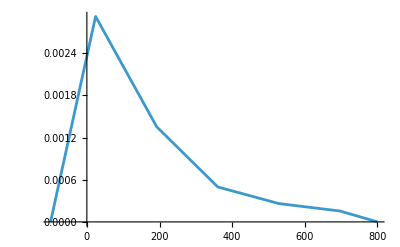

```mathematica
SmoothHistogram[generatedRTData,PlotRange->{{-100,800},All}]
```